```mathematica
?ScalarMixedSpins
```

package for scalar and mixed ...
Designations(7): d t it p pp collectPP pTimes
Symbolic(9): expandSigma expandSigTimes HBasis basisH coordinates matrixTransform fullCoordinates(...) fullTransform(...) RemBasis
Traces(4): fastTr1 fastTr fastTr10 gramMatrix symGramMatrix
RhoGen(16): lastKP firstKP nextKP listKPs compoze swapToPerm generateGroup normolizeKP KPToExpr invariantKPsets squareInvariantKPsets KPsetsToExpr rhoGen invariantKPTsets listKPTs allKPs depsGen
Linerear algebra(10): RowSimplify RowReduceUpTo RowReduceUpToShow RowReduceInfo LinDeps ApplyLinDeps LinDependent LinIndependent DeleteReduced
ExplicitMatrices(13): getSi getSz getSp getSm getSx getSy KP scalar scalarSparse mixed mixedSparse explicit explicitSparse
Utilities(5):  FE foundQ firstFound printTo plusToList getInt AndRuleDelayed

```mathematica
?collectPP
```

collectPP[expr] - take expr without pp[], put d[] and t[] (and it[]) into pp[] (orderless) and collect them

```mathematica
ADR=AndRuleDelayed
```

AndRuleDelayed

### 4 spins -2.1547 -> -2.0

```mathematica
τ=b0+b12 d[1,2]+b13 d[1,3]+b14 d[1,4]+b23 d[2,3]+b24 d[2,4]+b34 d[3,4] +bb1 d[1,2]d[3,4]+bb2 d[1,3]d[2,4]+bb3 d[1,4]d[2,3]/.{b34->b12,b24->b13}
```

b0+b12 d[1,2]+b13 d[1,3]+b14 d[1,4]+b23 d[2,3]+bb3 d[1,4] d[2,3]+b13 d[2,4]+bb2 d[1,3] d[2,4]+b12 d[3,4]+bb1 d[1,2] d[3,4]

```mathematica
Sort[{b0,b12,b13,b14,b23,bb1,bb2,bb3}]
```

{b0,b12,b13,b14,b23,bb1,bb2,bb3}

```mathematica
ρ=expandSigTimes[τ,τ]
```

b0^2+6 b12^2+6 b13^2+3 b14^2+3 b23^2+9 bb1^2+6 bb1 bb2+9 bb2^2+6 bb1 bb3+6 bb2 bb3+9 bb3^2+2 b0 b12 d[1,2]-2 b12^2 d[1,2]+2 b13 b14 d[1,2]+2 b13 b23 d[1,2]+6 b12 bb1 d[1,2]-6 bb1^2 d[1,2]+2 b12 bb2 d[1,2]-4 bb1 bb2 d[1,2]+2 b12 bb3 d[1,2]-4 bb1 bb3 d[1,2]+4 bb2 bb3 d[1,2]+2 b0 b13 d[1,3]-2 b13^2 d[1,3]+2 b12 b14 d[1,3]+2 b12 b23 d[1,3]+2 b13 bb1 d[1,3]+6 b13 bb2 d[1,3]-4 bb1 bb2 d[1,3]-6 bb2^2 d[1,3]+2 b13 bb3 d[1,3]+4 bb1 bb3 d[1,3]-4 bb2 bb3 d[1,3]+4 b12 b13 d[1,4]+2 b0 b14 d[1,4]-2 b14^2 d[1,4]+2 b23 bb1 d[1,4]+2 b23 bb2 d[1,4]+4 bb1 bb2 d[1,4]+6 b23 bb3 d[1,4]-4 bb1 bb3 d[1,4]-4 bb2 bb3 d[1,4]-6 bb3^2 d[1,4]+4 b12 b13 d[2,3]+2 b0 b23 d[2,3]-2 b23^2 d[2,3]+2 b14 bb1 d[2,3]+2 b14 bb2 d[2,3]+4 bb1 bb2 d[2,3]+6 b14 bb3 d[2,3]-4 bb1 bb3 d[2,3]-4 bb2 bb3 d[2,3]-6 bb3^2 d[2,3]+2 b14 b23 d[1,4] d[2,3]+4 b13 bb1 d[1,4] d[2,3]-2 b14 bb1 d[1,4] d[2,3]-2 b23 bb1 d[1,4] d[2,3]+4 b12 bb2 d[1,4] d[2,3]-2 b14 bb2 d[1,4] d[2,3]-2 b23 bb2 d[1,4] d[2,3]+2 b0 bb3 d[1,4] d[2,3]-4 b14 bb3 d[1,4] d[2,3]-4 b23 bb3 d[1,4] d[2,3]+2 bb1 bb3 d[1,4] d[2,3]+2 bb2 bb3 d[1,4] d[2,3]+4 bb3^2 d[1,4] d[2,3]+2 b0 b13 d[2,4]-2 b13^2 d[2,4]+2 b12 b14 d[2,4]+2 b12 b23 d[2,4]+2 b13 bb1 d[2,4]+6 b13 bb2 d[2,4]-4 bb1 bb2 d[2,4]-6 bb2^2 d[2,4]+2 b13 bb3 d[2,4]+4 bb1 bb3 d[2,4]-4 bb2 bb3 d[2,4]+2 b13^2 d[1,3] d[2,4]-4 b13 bb1 d[1,3] d[2,4]+2 b14 bb1 d[1,3] d[2,4]+2 b23 bb1 d[1,3] d[2,4]+2 b0 bb2 d[1,3] d[2,4]-8 b13 bb2 d[1,3] d[2,4]+2 bb1 bb2 d[1,3] d[2,4]+4 bb2^2 d[1,3] d[2,4]+4 b12 bb3 d[1,3] d[2,4]-4 b13 bb3 d[1,3] d[2,4]+2 bb2 bb3 d[1,3] d[2,4]+2 b0 b12 d[3,4]-2 b12^2 d[3,4]+2 b13 b14 d[3,4]+2 b13 b23 d[3,4]+6 b12 bb1 d[3,4]-6 bb1^2 d[3,4]+2 b12 bb2 d[3,4]-4 bb1 bb2 d[3,4]+2 b12 bb3 d[3,4]-4 bb1 bb3 d[3,4]+4 bb2 bb3 d[3,4]+2 b12^2 d[1,2] d[3,4]+2 b0 bb1 d[1,2] d[3,4]-8 b12 bb1 d[1,2] d[3,4]+4 bb1^2 d[1,2] d[3,4]-4 b12 bb2 d[1,2] d[3,4]+2 b14 bb2 d[1,2] d[3,4]+2 b23 bb2 d[1,2] d[3,4]+2 bb1 bb2 d[1,2] d[3,4]-4 b12 bb3 d[1,2] d[3,4]+4 b13 bb3 d[1,2] d[3,4]+2 bb1 bb3 d[1,2] d[3,4]

```mathematica
mt=explicit[1/2,4,τ];
mr=explicit[1/2,4,ρ];
Expand[mr]===Expand[mt.mt]
```

True

```mathematica
a0=collectPP[ρ]/.pp[__]->0/.pp[]->1;
a12=collectPP[ρ]/.{pp[]->0,pp[_,_]->0,pp[x_/;!MatchQ[x,d[1,2]]]->0}/.pp[__]->1;
a13=collectPP[ρ]/.{pp[]->0,pp[_,_]->0,pp[x_/;!MatchQ[x,d[1,3]]]->0}/.pp[__]->1;
a14=collectPP[ρ]/.{pp[]->0,pp[_,_]->0,pp[x_/;!MatchQ[x,d[1,4]]]->0}/.pp[__]->1;
a23=collectPP[ρ]/.{pp[]->0,pp[_,_]->0,pp[x_/;!MatchQ[x,d[2,3]]]->0}/.pp[__]->1;
a24=collectPP[ρ]/.{pp[]->0,pp[_,_]->0,pp[x_/;!MatchQ[x,d[2,4]]]->0}/.pp[__]->1;
a34=collectPP[ρ]/.{pp[]->0,pp[_,_]->0,pp[x_/;!MatchQ[x,d[3,4]]]->0}/.pp[__]->1;
a1=collectPP[ρ]/.ADR[pp[___],Except[pp[d[1,2],d[3,4]]],0]/.pp[__]->1;
a2=collectPP[ρ]/.ADR[pp[___],Except[pp[d[1,3],d[2,4]]],0]/.pp[__]->1;
a3=collectPP[ρ]/.ADR[pp[___],Except[pp[d[1,4],d[2,3]]],0]/.pp[__]->1;
```

```mathematica
a34=collectPP[ρ]/.{pp[]->0,pp[_,_]->0,pp[x_/;!MatchQ[x,d[3,4]]]->0}/.pp[__]->1;
```

```mathematica
a12-a34
```

0

```mathematica
H=d[1,2]+d[2,3]+d[3,4]
```

d[1,2]+d[2,3]+d[3,4]

```mathematica
a0
```

b0^2+6 b12^2+6 b13^2+3 b14^2+3 b23^2+9 bb1^2+6 bb1 bb2+9 bb2^2+6 bb1 bb3+6 bb2 bb3+9 bb3^2

```mathematica
ρ//collectPP
```

(b0^2+6 b12^2+6 b13^2+3 b14^2+3 b23^2+9 bb1^2+6 bb1 bb2+9 bb2^2+6 bb1 bb3+6 bb2 bb3+9 bb3^2) pp[]+(2 b0 b12-2 b12^2+2 b13 b14+2 b13 b23+6 b12 bb1-6 bb1^2+2 b12 bb2-4 bb1 bb2+2 b12 bb3-4 bb1 bb3+4 bb2 bb3) pp[d[1,2]]+(2 b0 b13-2 b13^2+2 b12 b14+2 b12 b23+2 b13 bb1+6 b13 bb2-4 bb1 bb2-6 bb2^2+2 b13 bb3+4 bb1 bb3-4 bb2 bb3) pp[d[1,3]]+(4 b12 b13+2 b0 b14-2 b14^2+2 b23 bb1+2 b23 bb2+4 bb1 bb2+6 b23 bb3-4 bb1 bb3-4 bb2 bb3-6 bb3^2) pp[d[1,4]]+(4 b12 b13+2 b0 b23-2 b23^2+2 b14 bb1+2 b14 bb2+4 bb1 bb2+6 b14 bb3-4 bb1 bb3-4 bb2 bb3-6 bb3^2) pp[d[2,3]]+(2 b0 b13-2 b13^2+2 b12 b14+2 b12 b23+2 b13 bb1+6 b13 bb2-4 bb1 bb2-6 bb2^2+2 b13 bb3+4 bb1 bb3-4 bb2 bb3) pp[d[2,4]]+(2 b0 b12-2 b12^2+2 b13 b14+2 b13 b23+6 b12 bb1-6 bb1^2+2 b12 bb2-4 bb1 bb2+2 b12 bb3-4 bb1 bb3+4 bb2 bb3) pp[d[3,4]]+(2 b12^2+2 b0 bb1-8 b12 bb1+4 bb1^2-4 b12 bb2+2 b14 bb2+2 b23 bb2+2 bb1 bb2-4 b12 bb3+4 b13 bb3+2 bb1 bb3) pp[d[1,2],d[3,4]]+(2 b13^2-4 b13 bb1+2 b14 bb1+2 b23 bb1+2 b0 bb2-8 b13 bb2+2 bb1 bb2+4 bb2^2+4 b12 bb3-4 b13 bb3+2 bb2 bb3) pp[d[1,3],d[2,4]]+(2 b14 b23+4 b13 bb1-2 b14 bb1-2 b23 bb1+4 b12 bb2-2 b14 bb2-2 b23 bb2+2 b0 bb3-4 b14 bb3-4 b23 bb3+2 bb1 bb3+2 bb2 bb3+4 bb3^2) pp[d[1,4],d[2,3]]

```mathematica
fastTr[H,ρ](* !!!! error, need to debug *)
```

0

```mathematica
func=collectPP[expandSigTimes[H,ρ]]/.ADR[pp[___],Except[pp[]],0]/.pp[___]->1
```

checked

Раскрыли d,t

Отсортировали

Раскрыли Паули и Леви-Чевиты

упростили кронекеры

sigma expanded

12 b0 b12-12 b12^2+12 b12 b13+12 b13 b14+6 b0 b23+12 b13 b23-6 b23^2+36 b12 bb1+6 b14 bb1-36 bb1^2+12 b12 bb2+6 b14 bb2-12 bb1 bb2+12 b12 bb3+18 b14 bb3-36 bb1 bb3+12 bb2 bb3-18 bb3^2

```mathematica
mH=explicit[1/2,4,H];
mr=explicit[1/2,4,ρ];
mHr=explicit[1/2,4,expandSigTimes[H,ρ]];
Expand[mHr]===Expand[mH.mr]
```

checked

Раскрыли d,t

Отсортировали

Раскрыли Паули и Леви-Чевиты

упростили кронекеры

sigma expanded

True

```mathematica
Clear[m1];
NN=8;
mm1=Table[Subscript[m1, i,j],{i,1,NN},{j,1,NN}];
Do[If[j<i,mm1[[i,j]]=Subscript[m1, j,i]],{i,1,NN},{j,1,NN}];
mm1//TableForm
```

m1_(1,1) | m1_(1,2) | m1_(1,3) | m1_(1,4) | m1_(1,5) | m1_(1,6) | m1_(1,7) | m1_(1,8)
m1_(1,2) | m1_(2,2) | m1_(2,3) | m1_(2,4) | m1_(2,5) | m1_(2,6) | m1_(2,7) | m1_(2,8)
m1_(1,3) | m1_(2,3) | m1_(3,3) | m1_(3,4) | m1_(3,5) | m1_(3,6) | m1_(3,7) | m1_(3,8)
m1_(1,4) | m1_(2,4) | m1_(3,4) | m1_(4,4) | m1_(4,5) | m1_(4,6) | m1_(4,7) | m1_(4,8)
m1_(1,5) | m1_(2,5) | m1_(3,5) | m1_(4,5) | m1_(5,5) | m1_(5,6) | m1_(5,7) | m1_(5,8)
m1_(1,6) | m1_(2,6) | m1_(3,6) | m1_(4,6) | m1_(5,6) | m1_(6,6) | m1_(6,7) | m1_(6,8)
m1_(1,7) | m1_(2,7) | m1_(3,7) | m1_(4,7) | m1_(5,7) | m1_(6,7) | m1_(7,7) | m1_(7,8)
m1_(1,8) | m1_(2,8) | m1_(3,8) | m1_(4,8) | m1_(5,8) | m1_(6,8) | m1_(7,8) | m1_(8,8)

```mathematica
bbb={b0,b12,b13,b14,b23,bb1,bb2,bb3}
```

{b0,b12,b13,b14,b23,bb1,bb2,bb3}

```mathematica
(FF=mm1/.SolveAlways[func==bbb.mm1.bbb,bbb][[1]])//MatrixForm
```

(0 | 6 | 0 | 0 | 3 | 0 | 0 | 0
6 | -12 | 6 | 0 | 0 | 18 | 6 | 6
0 | 6 | 0 | 6 | 6 | 0 | 0 | 0
0 | 0 | 6 | 0 | 0 | 3 | 3 | 9
3 | 0 | 6 | 0 | -6 | 0 | 0 | 0
0 | 18 | 0 | 3 | 0 | -36 | -6 | -18
0 | 6 | 0 | 3 | 0 | -6 | 0 | 6
0 | 6 | 0 | 9 | 0 | -18 | 6 | -18)

```mathematica
(NO=mm1/.SolveAlways[a0==bbb.mm1.bbb,bbb][[1]])//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 6 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 9 | 3 | 3
0 | 0 | 0 | 0 | 0 | 3 | 9 | 3
0 | 0 | 0 | 0 | 0 | 3 | 3 | 9)

```mathematica
(CC=mm1/.SolveAlways[(a12-a23)==bbb.mm1.bbb,bbb][[1]])//MatrixForm
```

(0 | 1 | 0 | 0 | -1 | 0 | 0 | 0
1 | -2 | -2 | 0 | 0 | 3 | 1 | 1
0 | -2 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | -1 | -1 | -3
-1 | 0 | 1 | 0 | 2 | 0 | 0 | 0
0 | 3 | 0 | -1 | 0 | -6 | -4 | 0
0 | 1 | 0 | -1 | 0 | -4 | 0 | 4
0 | 1 | 0 | -3 | 0 | 0 | 4 | 6)

```mathematica
Eigensystem[m123//N]
```

{{-9.64746,9.32858,3.12444,-3.12252,1.63186,-1.31489,8.88178×10^-15,1.2837×10^-16},{{-0.0419068,0.392554,0.094839,-0.118108,-0.0117404,-0.805666,-0.410716,0.057261},{0.0121328,0.103776,-0.0567969,-0.312877,-0.00940561,-0.0723079,0.433146,0.833687},{-0.328289,-0.316681,0.468984,0.122912,0.70904,-0.179806,0.141919,0.0409464},{0.227202,-0.567076,-0.502089,0.291263,0.142369,-0.182223,-0.367037,0.318883},{0.109795,-0.383481,0.316928,0.312873,-0.562651,-0.401706,0.400613,-0.0641816},{0.369629,-0.352083,-0.0743666,-0.740322,0.13394,-0.189653,0.143154,-0.333771},{0.221349,-0.199215,0.619779,-0.199215,-0.199215,0.287754,-0.531239,0.287754},{0.800641,0.320256,0.160128,0.320256,0.320256,-3.27172×10^-18,0.160128,0.}}}

```mathematica
NMinimize[func/a0,bbb]
```

{-6.4641,{b0→-3.9743,b12→3.61933,b13→-0.969795,b14→1.32477,b23→1.32477,bb1→-3.61933,bb2→0.969795,bb3→-1.32477}}

```mathematica
-6.464101615137753/3
```

-2.1547

```mathematica
NMinimize[{func/a0,a12==a23},bbb]
```

{-6.,{b0→1.72662,b12→-1.1511,b13→0.575551,b14→-1.15112,b23→-1.15107,bb1→1.15112,bb2→-0.575561,bb3→1.15112}}

```mathematica
Urs=((FF+λ0 NO+λ1 CC).bbb)~FE~(#==0&);
AppendTo[Urs,bbb.NO.bbb==1];
AppendTo[Urs,bbb.CC.bbb==0];
Urs//TableForm
```

b0 λ0+b23 (3-λ1)+b12 (6+λ1)==0
b13 (6-2 λ1)+b12 (-12+6 λ0-2 λ1)+b0 (6+λ1)+bb2 (6+λ1)+bb3 (6+λ1)+bb1 (18+3 λ1)==0
6 b13 λ0+b12 (6-2 λ1)+b14 (6+λ1)+b23 (6+λ1)==0
3 b14 λ0+bb3 (9-3 λ1)+bb1 (3-λ1)+bb2 (3-λ1)+b13 (6+λ1)==0
b0 (3-λ1)+b13 (6+λ1)+b23 (-6+3 λ0+2 λ1)==0
bb3 (-18+3 λ0)+bb1 (-36+9 λ0-6 λ1)+bb2 (-6+3 λ0-4 λ1)+b14 (3-λ1)+b12 (18+3 λ1)==0
9 bb2 λ0+bb1 (-6+3 λ0-4 λ1)+b14 (3-λ1)+b12 (6+λ1)+bb3 (6+3 λ0+4 λ1)==0
bb1 (-18+3 λ0)+b14 (9-3 λ1)+b12 (6+λ1)+bb2 (6+3 λ0+4 λ1)+bb3 (-18+9 λ0+6 λ1)==0
b0^2+6 b12^2+6 b13^2+3 b14^2+3 b23^2+bb1 (9 bb1+3 bb2+3 bb3)+bb2 (3 bb1+9 bb2+3 bb3)+bb3 (3 bb1+3 bb2+9 bb3)==1
b0 (b12-b23)+b13 (-2 b12+b14+b23)+b23 (-b0+b13+2 b23)+bb1 (3 b12-b14-6 bb1-4 bb2)+b14 (b13-bb1-bb2-3 bb3)+b12 (b0-2 b12-2 b13+3 bb1+bb2+bb3)+bb2 (b12-b14-4 bb1+4 bb3)+bb3 (b12-3 b14+4 bb2+6 bb3)==0

```mathematica
vars=bbb;
AppendTo[vars,λ0];
AppendTo[vars,λ1];
vars
```

{b0,b12,b13,b14,b23,bb1,bb2,bb3,λ0,λ1}

```mathematica
ares=Solve[Urs,vars];
```

$Aborted

```mathematica
res=NSolve[Urs,vars];
```

```mathematica
res//Length
```

57

```mathematica
(res2=Table[{Re[func/.res[[i]]],Im[func/.res[[i]]]//Abs},{i,1,Length[res]}]//SortBy[First])//TableForm
```

-6. | 0
-3. | 1.49277×10^-7
-3. | 3.05991×10^-9
-3. | 6.50426×10^-10
-3. | 2.15771×10^-16
-3. | 2.30107×10^-10
-3. | 2.22495×10^-10
-3. | 1.32378×10^-11
-3. | 3.0328×10^-11
-3. | 4.91268×10^-12
-3. | 5.69322×10^-13
-3. | 4.99228×10^-12
-3. | 3.19326×10^-11
-3. | 1.00646×10^-10
-3. | 8.99963×10^-11
-3. | 2.40054×10^-16
-1.36364 | 0.771389
-1.36364 | 0.771389
-1.36364 | 0.771389
-1.36364 | 0.771389
-1.36364 | 0.771389
-1.36364 | 0.771389
-1.36364 | 0.771389
-1.36364 | 0.771389
-1. | 0
-1. | 0
-1. | 0
-1. | 0
-1.49543×10^-12 | 5.65258×10^-14
-5.8987×10^-13 | 6.40738×10^-14
1.84119×10^-13 | 1.68067×10^-13
2.08734×10^-13 | 8.36352×10^-13
3.2511×10^-13 | 5.08059×10^-13
5.30844×10^-13 | 1.05691×10^-12
1.8 | 0
1.8 | 0
3. | 5.12766×10^-8
3. | 5.33459×10^-10
3. | 2.25965×10^-10
3. | 7.65128×10^-11
3. | 4.79191×10^-11
3. | 2.61899×10^-15
3. | 2.222×10^-15
3. | 2.46146×10^-15
3. | 2.24742×10^-15
3. | 1.70391×10^-15
3. | 2.15337×10^-15
3. | 1.38784×10^-10
3. | 1.5485×10^-10
3. | 1.49019×10^-15
3. | 2.25463×10^-15
3. | 1.61495×10^-11
3. | 5.94127×10^-11
3. | 1.41303×10^-10
3. | 4.07235×10^-7
3. | 9.92267×10^-7
3.00001 | 2.26697×10^-6

### 5 spins -1.92789 -> -1.86852

```mathematica
groupl5=generateGroup[{{1->5,2->4,3->3,4->2,5->1}}]//Keys
```

{{1→5,2→4,3→3,4→2,5→1},{1→1,2→2,3→3,4→4,5→5}}

```mathematica
basisl5={1};
AppendTo[basisl5,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[1,5,groupl5]];
AppendTo[basisl5,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[2,5,groupl5]];
(basisl5=basisl5//Flatten)//TableForm;
{Table[i,{i,1,Length[basisl5]}],basisl5}//Transpose//TableForm
```

1 | 1
2 | d[1,2]+d[4,5]
3 | d[1,3]+d[3,5]
4 | d[1,4]+d[2,5]
5 | d[1,5]
6 | d[2,3]+d[3,4]
7 | d[2,4]
8 | d[1,3] d[2,4]+d[2,4] d[3,5]
9 | d[1,3] d[2,5]+d[1,4] d[3,5]
10 | d[1,4] d[2,3]+d[2,5] d[3,4]
11 | d[1,4] d[2,5]
12 | d[1,5] d[2,3]+d[1,5] d[3,4]
13 | d[1,5] d[2,4]
14 | d[1,2] d[3,4]+d[2,3] d[4,5]
15 | d[1,2] d[3,5]+d[1,3] d[4,5]
16 | d[1,2] d[4,5]

```mathematica
cluster5={{1,2,3,4,5}}
```

{{1,2,3,4,5}}

```mathematica
basis5var={1};
AppendTo[basis5var,(Plus@@#&)/@(KPToExpr/@#&)/@squareInvariantKPsets[1,cluster5]];
AppendTo[basis5var,(Plus@@#&)/@(KPToExpr/@#&)/@squareInvariantKPsets[2,cluster5]];
basis5var=basis5var//Flatten;
{Table[i,{i,1,Length[basis5var]}],basis5var}//Transpose//TableForm
```

1 | 1
2 | d[1,2]+d[2,3]+d[3,4]+d[4,5]
3 | d[1,3]+d[2,4]+d[3,5]
4 | d[1,4]+d[2,5]
5 | d[1,5]
6 | d[1,3] d[2,4]+d[2,4] d[3,5]
7 | d[1,3] d[2,5]+d[1,4] d[3,5]
8 | d[1,4] d[2,3]+d[2,5] d[3,4]
9 | d[1,4] d[2,5]
10 | d[1,5] d[2,3]+d[1,5] d[3,4]
11 | d[1,5] d[2,4]
12 | d[1,2] d[3,4]+d[2,3] d[4,5]
13 | d[1,2] d[3,5]+d[1,3] d[4,5]
14 | d[1,2] d[4,5]

```mathematica
Clear[b5]
```

```mathematica
bb5={b0,b1,b2,b3,b4,b5,b6,b7,b8,b9,b10,b11,b12,b13,b14,b15}(*Table[Subscript[b, i],{i,0,15}]*)
```

{b0,b1,b2,b3,b4,b5,b6,b7,b8,b9,b10,b11,b12,b13,b14,b15}

```mathematica
τ5=basisl5.bb5//Expand
```

b0+b1 d[1,2]+b2 d[1,3]+b3 d[1,4]+b4 d[1,5]+b5 d[2,3]+b9 d[1,4] d[2,3]+b11 d[1,5] d[2,3]+b6 d[2,4]+b7 d[1,3] d[2,4]+b12 d[1,5] d[2,4]+b3 d[2,5]+b8 d[1,3] d[2,5]+b10 d[1,4] d[2,5]+b5 d[3,4]+b13 d[1,2] d[3,4]+b11 d[1,5] d[3,4]+b9 d[2,5] d[3,4]+b2 d[3,5]+b14 d[1,2] d[3,5]+b8 d[1,4] d[3,5]+b7 d[2,4] d[3,5]+b1 d[4,5]+b15 d[1,2] d[4,5]+b14 d[1,3] d[4,5]+b13 d[2,3] d[4,5]

```mathematica
Hl5=basisl5[[2]]+basisl5[[6]]
```

d[1,2]+d[2,3]+d[3,4]+d[4,5]

```mathematica
ρ5=expandSigTimes[τ5,τ5]
```

checked

Раскрыли d,t

Отсортировали

Раскрыли Паули и Леви-Чевиты

упростили кронекеры

sigma expanded

b0^2+6 b1^2+9 b10^2+18 b11^2+6 b10 b12+9 b12^2+18 b13^2+12 b11 b14+18 b14^2+6 b10 b15+6 b12 b15+9 b15^2+1248+ⅈ b14 b9 d[1,5] t[2,3,4]-ⅈ b15 b9 d[1,5] t[2,3,4]+ⅈ b10 b7 d[1,4] t[2,3,5]+ⅈ b13 b7 d[1,4] t[2,3,5]-ⅈ b13 b8 d[1,4] t[2,3,5]+ⅈ b11 b9 d[1,4] t[2,3,5]-ⅈ b12 b9 d[1,4] t[2,3,5]-ⅈ b7 b9 d[1,4] t[2,3,5]-ⅈ b11 b7 d[1,3] t[2,4,5]+ⅈ b8 b9 d[1,3] t[2,4,5]
 |  |  |  |

```mathematica
mt=explicit[1/2,5,τ5];
mr=explicit[1/2,5,ρ5];
Expand[mr]===Expand[mt.mt]
```

True

```mathematica
fastTr[Hl5,ρ5](* !!!! error, need to debug *)
```

0

```mathematica
func5=collectPP[expandSigTimes[Hl5,ρ5]]/.ADR[pp[___],Except[pp[]],0]/.pp[___]->1
```

checked

Раскрыли d,t

Отсортировали

Раскрыли Паули и Леви-Чевиты

упростили кронекеры

sigma expanded

12 b0 b1-12 b1^2+12 b1 b10+12 b10 b11-36 b11^2+12 b1 b12+24 b10 b12+36 b11 b12+36 b1 b13+12 b11 b13-72 b13^2+12 b10 b14-48 b11 b14+12 b12 b14+36 b13 b14-36 b14^2+36 b1 b15-24 b10 b15+12 b11 b15-24 b12 b15+36 b14 b15-36 b15^2+12 b1 b2+12 b11 b2+36 b14 b2+12 b13 b3+12 b2 b3+36 b11 b4+12 b14 b4+12 b3 b4+12 b0 b5+36 b13 b5+12 b2 b5-12 b5^2+12 b3 b6+12 b5 b6+12 b1 b7+12 b11 b7-24 b13 b7+12 b14 b7+12 b3 b7+12 b5 b7+36 b10 b8+12 b12 b8+12 b13 b8+12 b15 b8+12 b2 b8+12 b4 b8+36 b7 b8+12 b1 b9+36 b11 b9-72 b13 b9+12 b14 b9+36 b3 b9+12 b5 b9+24 b7 b9+12 b8 b9-36 b9^2

```mathematica
mH=explicit[1/2,5,Hl5];
mr=explicit[1/2,5,ρ5];
mHr=explicit[1/2,5,expandSigTimes[Hl5,ρ5]];
Expand[mHr]===Expand[mH.mr]
```

checked

Раскрыли d,t

Отсортировали

Раскрыли Паули и Леви-Чевиты

упростили кронекеры

sigma expanded

True

```mathematica
basisl5s=basisl5~FE~((#//plusToList//First//collectPP)&);
(a5=Table[collectPP[ρ5]/.ADR[pp[___],Except[basisl5s[[i]]],0]/.pp[___]->1,{i,1,16}])//TableForm
```

b0^2+6 b1^2+9 b10^2+18 b11^2+6 b10 b12+9 b12^2+18 b13^2+12 b11 b14+18 b14^2+6 b10 b15+6 b12 b15+9 b15^2+6 b2^2+6 b3^2+3 b4^2+6 b5^2+3 b6^2+12 b13 b7+18 b7^2+12 b11 b8+12 b14 b8+18 b8^2+12 b13 b9+12 b7 b9+18 b9^2
2 b0 b1-2 b1^2+2 b1 b10+2 b1 b12+4 b10 b12+2 b11 b13-6 b13^2-4 b11 b14+6 b13 b14-6 b14^2+6 b1 b15-4 b10 b15-4 b12 b15-6 b15^2+2 b11 b2+6 b14 b2+2 b3 b4+6 b13 b5+2 b2 b5+2 b3 b6+2 b11 b7-4 b13 b7+2 b14 b7+2 b5 b7+4 b11 b8+2 b13 b8-4 b14 b8+2 b2 b8+6 b7 b8+6 b11 b9-4 b13 b9+2 b14 b9+2 b5 b9+4 b7 b9+2 b8 b9
2 b1 b11+2 b10 b13+2 b12 b13+6 b1 b14-6 b14^2+6 b13 b15+2 b0 b2-2 b2^2+2 b11 b3+2 b14 b3+2 b2 b4+2 b1 b5+2 b3 b5+2 b13 b6+2 b10 b7+6 b12 b7-4 b13 b7+2 b15 b7+6 b6 b7-6 b7^2+2 b1 b8-8 b14 b8+6 b3 b8-6 b8^2+6 b10 b9+2 b12 b9+4 b13 b9+2 b15 b9+2 b6 b9-4 b7 b9
-6 b10^2-4 b10 b12+6 b11 b13+4 b11 b14+2 b13 b14-4 b10 b15+4 b12 b15+2 b11 b2+2 b14 b2+2 b0 b3+6 b10 b3+2 b12 b3+2 b15 b3-2 b3^2+2 b1 b4+2 b13 b5+2 b2 b5+2 b1 b6+2 b11 b7+4 b13 b7+6 b14 b7+2 b5 b7-4 b11 b8+2 b13 b8-4 b14 b8+6 b2 b8+2 b7 b8-6 b8^2+2 b11 b9-4 b13 b9+2 b14 b9+6 b5 b9-4 b7 b9+6 b8 b9-6 b9^2
-12 b11^2-4 b10 b12-6 b12^2+2 b13^2-8 b11 b14+4 b10 b15-4 b12 b15+2 b2^2+4 b1 b3+2 b0 b4-2 b4^2+12 b11 b5+4 b14 b5+2 b10 b6+6 b12 b6+2 b15 b6+4 b13 b7+6 b7^2-8 b11 b8+8 b14 b8+4 b5 b8+12 b13 b9+4 b7 b9+2 b9^2
2 b10 b11-6 b11^2+6 b11 b12+6 b1 b13-6 b13^2+2 b10 b14-4 b11 b14+2 b12 b14+2 b11 b15+6 b14 b15+2 b1 b2+2 b13 b3+2 b2 b3+6 b11 b4+2 b14 b4+2 b0 b5-2 b5^2+2 b5 b6+2 b1 b7+2 b3 b7+6 b10 b8-4 b11 b8+2 b12 b8+4 b14 b8+2 b15 b8+2 b4 b8+2 b1 b9-8 b13 b9+6 b3 b9-6 b9^2
6 b11^2-4 b10 b12-6 b12^2+4 b11 b14+2 b14^2+4 b10 b15-4 b12 b15+4 b13 b2+4 b1 b3+2 b10 b4+6 b12 b4+2 b15 b4+2 b5^2+2 b0 b6-2 b6^2-8 b13 b7+12 b2 b7-12 b7^2+4 b11 b8+12 b14 b8+2 b8^2+8 b13 b9+4 b2 b9-8 b7 b9
2 b10 b13+2 b11 b13-2 b12 b13+2 b10 b14+2 b13 b14-2 b14^2+2 b12 b2-2 b13 b2+2 b13 b3+2 b14 b3+2 b13 b5-2 b13 b6+2 b2 b6+2 b0 b7-2 b10 b7-4 b12 b7+2 b13 b7-2 b15 b7-4 b2 b7+2 b4 b7-4 b6 b7+4 b7^2+2 b1 b8-2 b13 b8-4 b14 b8+2 b15 b8-2 b8^2+2 b1 b9+2 b11 b9-2 b12 b9-2 b14 b9+2 b15 b9-2 b2 b9+2 b5 b9-2 b6 b9+2 b7 b9+2 b8 b9
2 b1 b11-2 b10 b13-2 b11 b13+4 b12 b13+2 b13^2-2 b13 b14+2 b11 b15-2 b14 b2-2 b11 b3-2 b14 b3+2 b2 b3+2 b14 b4+2 b10 b5+2 b14 b5+2 b14 b6+2 b1 b7-2 b10 b7-2 b13 b7-4 b14 b7+2 b15 b7+2 b0 b8+2 b11 b8+2 b12 b8+4 b13 b8+2 b14 b8-2 b15 b8-4 b2 b8-4 b3 b8-2 b7 b8+4 b8^2-4 b10 b9+2 b11 b9-4 b12 b9-2 b14 b9+2 b3 b9+2 b7 b9
2 b1 b11-2 b10 b11-4 b11 b13-2 b10 b14-2 b11 b14+4 b12 b14-2 b13 b14+2 b14^2+2 b11 b15+2 b10 b2+2 b13 b2-2 b13 b3+2 b13 b4-2 b13 b5+2 b3 b5+2 b13 b6+2 b1 b7-2 b14 b7+2 b15 b7-2 b3 b7-4 b10 b8+2 b11 b8-4 b12 b8-2 b13 b8+2 b3 b8+2 b7 b8+2 b0 b9-2 b11 b9+2 b12 b9+2 b13 b9+4 b14 b9-2 b15 b9-4 b3 b9-4 b5 b9+2 b7 b9+4 b9^2
2 b0 b10+4 b10^2+4 b1 b12+2 b10 b12+4 b11 b13-2 b13^2+4 b11 b14+4 b13 b14-2 b14^2+2 b10 b15-8 b10 b3-4 b12 b3-4 b15 b3+2 b3^2+2 b15 b4+2 b15 b6+4 b13 b7+4 b14 b7-4 b13 b8+4 b5 b8-4 b7 b8-4 b11 b9-4 b14 b9+4 b2 b9-8 b8 b9
2 b0 b11-2 b10 b11+4 b11^2-4 b11 b12+2 b10 b13-2 b13^2+2 b10 b14+2 b11 b14-2 b12 b14+2 b13 b14-2 b11 b15+2 b14 b2+2 b13 b3+2 b14 b3-4 b11 b4-2 b14 b4-4 b11 b5+2 b12 b5-2 b14 b5+2 b4 b5+2 b11 b6+2 b14 b7+2 b1 b8+2 b11 b8-2 b12 b8-2 b13 b8+2 b15 b8+2 b2 b8-2 b4 b8-2 b5 b8+2 b7 b8+2 b1 b9-4 b13 b9-2 b14 b9+2 b15 b9+2 b8 b9-2 b9^2
4 b1 b10-4 b11^2+2 b0 b12+2 b10 b12+4 b12^2+2 b13^2-4 b11 b14-4 b13 b14+2 b14^2+2 b12 b15+4 b15 b3-2 b10 b4-4 b12 b4-2 b15 b4+4 b11 b5-2 b10 b6-4 b12 b6-2 b15 b6+2 b4 b6-4 b13 b7+4 b2 b7-4 b7^2-4 b11 b8+8 b13 b8+2 b8^2+8 b14 b9-4 b7 b9-4 b8 b9+2 b9^2
2 b10 b11+2 b0 b13-4 b1 b13-2 b10 b13-2 b11 b13+2 b12 b13+4 b13^2+2 b1 b14+2 b11 b14-4 b12 b14-2 b11 b15-4 b14 b15+2 b15 b2+2 b11 b3+2 b1 b5-4 b13 b5-2 b1 b7+2 b10 b7+2 b13 b7+2 b14 b7+2 b3 b7-2 b11 b8+4 b12 b8+4 b13 b8-2 b15 b8-2 b7 b8+2 b8^2-2 b1 b9-4 b11 b9+2 b13 b9-2 b14 b9+2 b2 b9+2 b4 b9-2 b5 b9+2 b6 b9-2 b8 b9
-2 b1 b11+2 b10 b11+2 b1 b13+2 b11 b13-4 b12 b13+2 b0 b14-4 b1 b14-2 b10 b14+2 b11 b14+2 b12 b14+4 b14^2-4 b13 b15+2 b1 b2-4 b14 b2+2 b11 b3+2 b15 b5+2 b10 b7+2 b13 b7-2 b14 b7-2 b15 b7+2 b3 b7-2 b1 b8-2 b13 b8+2 b14 b8-2 b2 b8+2 b4 b8+2 b5 b8+2 b6 b8-4 b7 b8-2 b11 b9+4 b12 b9+4 b14 b9-2 b15 b9-2 b7 b9-2 b8 b9+2 b9^2
2 b1^2-4 b1 b10-4 b1 b12-4 b11 b13-8 b13 b14+2 b0 b15-8 b1 b15+2 b10 b15+2 b12 b15+4 b15^2+4 b13 b2+4 b12 b3+2 b10 b4+4 b14 b5+2 b10 b6-4 b14 b7+4 b11 b8-4 b13 b8+4 b7 b8-2 b8^2+4 b11 b9-4 b14 b9+4 b7 b9+4 b8 b9-2 b9^2

```mathematica
(FF5=CoefficientArrays[func5,bb5,"Symmetric"->True]//Last//Normal)//MatrixForm
```

(0 | 6 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6 | -12 | 6 | 0 | 0 | 0 | 0 | 6 | 0 | 6 | 6 | 0 | 6 | 18 | 0 | 18
0 | 6 | 0 | 6 | 0 | 6 | 0 | 0 | 6 | 0 | 0 | 6 | 0 | 0 | 18 | 0
0 | 0 | 6 | 0 | 6 | 0 | 6 | 6 | 0 | 18 | 0 | 0 | 0 | 6 | 0 | 0
0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 18 | 0 | 0 | 6 | 0
6 | 0 | 6 | 0 | 0 | -12 | 6 | 6 | 0 | 6 | 0 | 0 | 0 | 18 | 0 | 0
0 | 0 | 0 | 6 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6 | 0 | 6 | 0 | 6 | 0 | 0 | 18 | 12 | 0 | 6 | 0 | -12 | 6 | 0
0 | 0 | 6 | 0 | 6 | 0 | 0 | 18 | 0 | 6 | 18 | 0 | 6 | 6 | 0 | 6
0 | 6 | 0 | 18 | 0 | 6 | 0 | 12 | 6 | -36 | 0 | 18 | 0 | -36 | 6 | 0
0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 6 | 12 | 0 | 6 | -12
0 | 0 | 6 | 0 | 18 | 0 | 0 | 6 | 0 | 18 | 6 | -36 | 18 | 6 | -24 | 6
0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 12 | 18 | 0 | 0 | 6 | -12
0 | 18 | 0 | 6 | 0 | 18 | 0 | -12 | 6 | -36 | 0 | 6 | 0 | -72 | 18 | 0
0 | 0 | 18 | 0 | 6 | 0 | 0 | 6 | 0 | 6 | 6 | -24 | 6 | 18 | -36 | 18
0 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | -12 | 6 | -12 | 0 | 18 | -36)

```mathematica
a5m=Table[CoefficientArrays[a5[[i]],bb5,"Symmetric"->True]//Last//Normal,{i,1,16}];
```

```mathematica
a5m[[14]]-a5m[[8]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | -2 | 0 | 0 | 0 | -2 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 2 | 0 | 2 | 0 | 0 | -1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | -1 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | -3 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | 0
-1 | -1 | 2 | 1 | -1 | 0 | 2 | -4 | -1 | -1 | 2 | 0 | 2 | 0 | 1 | 1
0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 4 | -2 | 0 | -1 | 2 | 3 | 2 | -2
0 | -2 | 2 | 0 | 1 | -2 | 2 | -1 | -2 | 0 | 0 | -3 | 1 | 1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | -2 | -1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1 | -3 | 1 | 0 | 0 | -2 | 1 | -1
0 | 0 | -1 | 0 | 0 | 0 | 0 | 2 | 2 | 1 | 0 | 0 | 0 | 2 | -2 | 0
1 | -2 | 1 | -1 | 0 | -3 | 1 | 0 | 3 | 1 | -2 | -2 | 2 | 4 | -1 | 0
0 | 1 | 0 | -1 | 0 | 0 | 0 | 1 | 2 | 0 | -1 | 1 | -2 | -1 | 2 | -2
0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | -2 | -1 | 0 | -1 | 0 | 0 | -2 | 0)

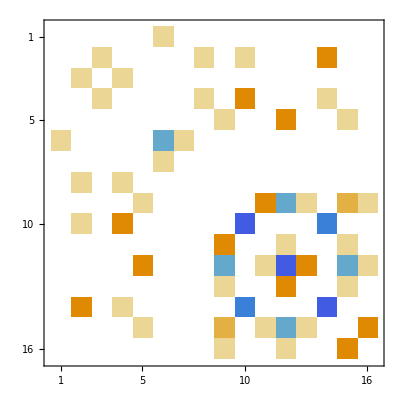

```mathematica
3a5m[[6]]//MatrixPlot
```

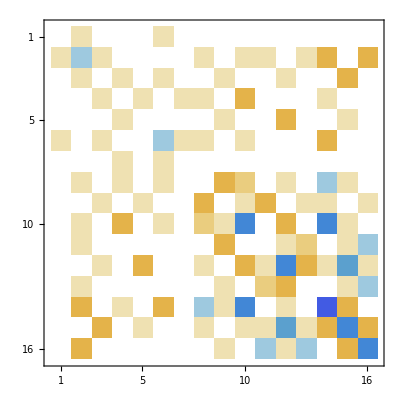

```mathematica
FF5-3 a5m[[2]]-3 a5m[[6]]//MatrixPlot
```

```mathematica
cluster5={{1,2,3,4,5}}
```

{{1,2,3,4,5}}

```mathematica
NMinimize[{func5/a5[[1]]},bb5]
```

{-7.71155,{b0→3.58717,b1→-2.77501,b2→1.05631,b3→-0.687325,b4→0.654281,b5→-1.83543,b6→0.654281,b7→-0.389561,b8→0.229108,b9→0.550013,b10→-0.0917971,b11→-0.389561,b12→0.124841,b13→1.67498,b14→-0.895859,b15→1.99589}}

```mathematica
-7.711545013271962/4
```

-1.92789

```mathematica
NMinimize[{func5/a5[[1]],a5[[2]]==a5[[6]]&&a5[[3]]==a5[[7]]},bb5]
```

{-7.47407,{b0→-0.296144,b1→0.18449,b2→-0.0821319,b3→0.0915366,b4→-0.082132,b5→0.184491,b6→-0.0822197,b7→0.0511467,b8→-0.0201828,b9→-0.0821533,b10→0.010803,b11→0.0511686,b12→-0.0202054,b13→-0.153506,b14→0.0511681,b15→-0.082155}}

```mathematica
-7.474068184959573/4
```

-1.86852

```mathematica
basisl5//TableForm
```

1
d[1,2]+d[4,5]
d[1,3]+d[3,5]
d[1,4]+d[2,5]
d[1,5]
d[2,3]+d[3,4]
d[2,4]
d[1,3] d[2,4]+d[2,4] d[3,5]
d[1,3] d[2,5]+d[1,4] d[3,5]
d[1,4] d[2,3]+d[2,5] d[3,4]
d[1,4] d[2,5]
d[1,5] d[2,3]+d[1,5] d[3,4]
d[1,5] d[2,4]
d[1,2] d[3,4]+d[2,3] d[4,5]
d[1,2] d[3,5]+d[1,3] d[4,5]
d[1,2] d[4,5]

```mathematica
basis5var={1};
AppendTo[basis5var,(Plus@@#&)/@(KPToExpr/@#&)/@squareInvariantKPsets[1,cluster5]];
AppendTo[basis5var,(Plus@@#&)/@(KPToExpr/@#&)/@squareInvariantKPsets[2,cluster5]];
(basis5var=basis5var//Flatten)//TableForm
```

1
d[1,2]+d[2,3]+d[3,4]+d[4,5]
d[1,3]+d[2,4]+d[3,5]
d[1,4]+d[2,5]
d[1,5]
d[1,3] d[2,4]+d[2,4] d[3,5]
d[1,3] d[2,5]+d[1,4] d[3,5]
d[1,4] d[2,3]+d[2,5] d[3,4]
d[1,4] d[2,5]
d[1,5] d[2,3]+d[1,5] d[3,4]
d[1,5] d[2,4]
d[1,2] d[3,4]+d[2,3] d[4,5]
d[1,2] d[3,5]+d[1,3] d[4,5]
d[1,2] d[4,5]

```mathematica
Urs5=((FF5+λ0 a5m[[1]]+λ1(a5m[[2]]-a5m[[6]])+λ2(a5m[[3]]-a5m[[7]])).bb5)~FE~(#==0&);
AppendTo[Urs5,bb5.a5m[[1]].bb5==1];
AppendTo[Urs5,bb5.(a5m[[2]]-a5m[[6]]).bb5==0];
AppendTo[Urs5,bb5.(a5m[[3]]-a5m[[7]]).bb5==0];
Urs5//TableForm
```

b0 λ0+b5 (6-λ1)+b1 (6+λ1)+b2 λ2-b6 λ2==0
b13 (18-3 λ1)+b1 (-12+6 λ0-2 λ1)+b2 (6-λ1)+b7 (6-λ1)+b9 (6-λ1)+b0 (6+λ1)+b10 (6+λ1)+b12 (6+λ1)+b15 (18+3 λ1)+b11 λ2+3 b14 λ2-2 b3 λ2+b5 λ2+b8 λ2==0
b1 (6-λ1)+b3 (6-λ1)+b11 (6+λ1)+b5 (6+λ1)+b8 (6+λ1)+b14 (18+3 λ1)+b2 (6 λ0-2 λ2)+b0 λ2-2 b13 λ2+b4 λ2-6 b7 λ2-2 b9 λ2==0
6 b3 λ0+b9 (18-3 λ1)+b13 (6-λ1)+b2 (6-λ1)+b7 (6-λ1)+b4 (6+λ1)+b6 (6+λ1)-2 b1 λ2+b11 λ2+b14 λ2+b5 λ2+3 b8 λ2==0
3 b4 λ0+b11 (18-3 λ1)+b14 (6-λ1)+b8 (6-λ1)+b3 (6+λ1)-b10 λ2-3 b12 λ2-b15 λ2+b2 λ2==0
b0 (6-λ1)+b6 (6-λ1)+b2 (6+λ1)+b7 (6+λ1)+b9 (6+λ1)+b13 (18+3 λ1)+b5 (-12+6 λ0+2 λ1-2 λ2)+b1 λ2+b3 λ2==0
b5 (6-λ1)+b3 (6+λ1)-b0 λ2+b13 λ2+3 b7 λ2+b9 λ2+b6 (3 λ0+2 λ2)==0
b1 (6-λ1)+b3 (6-λ1)+b11 (6+λ1)+b14 (6+λ1)+b5 (6+λ1)+b8 (18+3 λ1)+b10 λ2+3 b12 λ2+b15 λ2-6 b2 λ2+3 b6 λ2+b13 (-12+6 λ0-2 λ1+2 λ2)+b9 (12+6 λ0+2 λ1+2 λ2)+b7 (18 λ0+6 λ2)==0
b10 (18-3 λ1)+b12 (6-λ1)+b15 (6-λ1)+b4 (6-λ1)+b13 (6+λ1)+b2 (6+λ1)+b9 (6+λ1)+b7 (18+3 λ1)+b14 (6 λ0-4 λ1-10 λ2)+b8 (18 λ0-8 λ2)+b11 (6 λ0+4 λ1-2 λ2)+b1 λ2+3 b3 λ2==0
b3 (18-3 λ1)+b1 (6-λ1)+b14 (6+λ1)+b5 (6+λ1)+b8 (6+λ1)+b11 (18+3 λ1)+b9 (-36+18 λ0+6 λ1)+b13 (-36+6 λ0+2 λ1-2 λ2)+3 b10 λ2+b12 λ2+b15 λ2-2 b2 λ2+b6 λ2+b7 (12+6 λ0+2 λ1+2 λ2)==0
9 b10 λ0+b8 (18-3 λ1)+b11 (6-λ1)+b14 (6-λ1)+b1 (6+λ1)+b15 (-12+3 λ0-2 λ1-2 λ2)+b13 λ2-b4 λ2+b7 λ2+3 b9 λ2+b12 (12+3 λ0+2 λ1+2 λ2)==0
b12 (18-3 λ1)+b4 (18-3 λ1)+b10 (6-λ1)+b15 (6-λ1)+b13 (6+λ1)+b2 (6+λ1)+b7 (6+λ1)+b9 (18+3 λ1)+b11 (-36+18 λ0+6 λ1-6 λ2)+b14 (-24+6 λ0-2 λ2)+b8 (6 λ0+4 λ1-2 λ2)+b1 λ2+b3 λ2==0
b11 (18-3 λ1)+b14 (6-λ1)+b8 (6-λ1)+b1 (6+λ1)+b13 λ2-3 b4 λ2+3 b7 λ2+b9 λ2+b15 (-12+3 λ0-2 λ1+2 λ2)+b10 (12+3 λ0+2 λ1+2 λ2)+b12 (9 λ0+6 λ2)==0
b13 (-72+18 λ0)+b1 (18-3 λ1)+b3 (6-λ1)+b11 (6+λ1)+b8 (6+λ1)+b14 (18+3 λ1)+b5 (18+3 λ1)+b9 (-36+6 λ0+2 λ1-2 λ2)+b10 λ2+b12 λ2+3 b15 λ2-2 b2 λ2+b6 λ2+b7 (-12+6 λ0-2 λ1+2 λ2)==0
b15 (18-3 λ1)+b10 (6-λ1)+b12 (6-λ1)+b4 (6-λ1)+b7 (6+λ1)+b9 (6+λ1)+b13 (18+3 λ1)+b2 (18+3 λ1)+b8 (6 λ0-4 λ1-10 λ2)+b14 (-36+18 λ0-6 λ1-8 λ2)+b11 (-24+6 λ0-2 λ2)+3 b1 λ2+b3 λ2==0
b15 (-36+9 λ0-6 λ1)+b14 (18-3 λ1)+b11 (6-λ1)+b8 (6-λ1)+b1 (18+3 λ1)+b10 (-12+3 λ0-2 λ1-2 λ2)+3 b13 λ2-b4 λ2+b7 λ2+b9 λ2+b12 (-12+3 λ0-2 λ1+2 λ2)==0
b0^2+6 b1^2+b10 (9 b10+3 b12+3 b15)+b12 (3 b10+9 b12+3 b15)+b15 (3 b10+3 b12+9 b15)+6 b2^2+6 b3^2+3 b4^2+6 b5^2+3 b6^2+b11 (18 b11+6 b14+6 b8)+b14 (6 b11+18 b14+6 b8)+b8 (6 b11+6 b14+18 b8)+b13 (18 b13+6 b7+6 b9)+b7 (6 b13+18 b7+6 b9)+b9 (6 b13+6 b7+18 b9)==1
b0 (b1-b5)+(b3-b5) b6+b10 (b1-b11+2 b12-b14-2 b15-3 b8)+b15 (3 b1-2 b10-b11-2 b12-3 b14-6 b15-b8)+b12 (b1+2 b10-3 b11-b14-2 b15-b8)+b4 (-3 b11-b14+b3-b8)+b2 (-b1+b11+3 b14-b3+b5+b8)+b3 (-b13-b2+b4+b6-b7-3 b9)+b1 (b0-2 b1+b10+b12-3 b13+3 b15-b2-b7-b9)+b5 (-b0+3 b13+b2+2 b5-b6+b7+b9)+b8 (-3 b10+4 b11-b12+b13-4 b14-b15+b2-b4+3 b7+b9)+b14 (-b10-b12+3 b13-6 b14-3 b15+3 b2-b4+b7-4 b8+b9)+b13 (-3 b1+b11+3 b14-b3+3 b5-2 b7+b8+2 b9)+b7 (-b1+b11-2 b13+b14-b3+b5+3 b8+2 b9)+b11 (-b10+6 b11-3 b12+b13-b15+b2-3 b4+b7+4 b8+3 b9)+b9 (-b1+3 b11+2 b13+b14-3 b3+b5+2 b7+b8+6 b9)==0
(-b10-3 b12-b15+b2) b4+(b1+b3-2 b5) b5+b0 (b2-b6)+b14 (3 b1-2 b11-8 b14+b3-10 b8)+b11 (b1-6 b11-2 b14+b3-2 b8)+(b1-2 b11-10 b14+3 b3-8 b8) b8+b1 (b11+3 b14-2 b3+b5+b8)+b3 (-2 b1+b11+b14+b5+3 b8)+b2 (b0-2 b13-2 b2+b4-6 b7-2 b9)+b13 (b10+b12+3 b15-2 b2+b6+2 b7-2 b9)+(3 b10+b12-2 b13+b15-2 b2+b6+2 b7) b9+b15 (-2 b10+2 b12+3 b13-b4+b7+b9)+b12 (2 b10+6 b12+b13+2 b15-3 b4+3 b7+b9)+b6 (-b0+b13+2 b6+3 b7+b9)+b7 (b10+3 b12+2 b13+b15-6 b2+3 b6+6 b7+2 b9)+b10 (2 b12+b13-2 b15-b4+b7+3 b9)==0

```mathematica
vars5=bb5;
AppendTo[vars5,λ0];
AppendTo[vars5,λ1];
AppendTo[vars5,λ2];
vars5
```

{b0,b1,b2,b3,b4,b5,b6,b7,b8,b9,b10,b11,b12,b13,b14,b15,λ0,λ1,λ2}

```mathematica
res5=NSolve[Urs5,vars5];
```

$Aborted

### 6 spins -1.99486 -> -1.8685 ->

```mathematica
groupl6=generateGroup[{{1->6,2->5,3->4,4->3,5->2,6->1}}]//Keys
```

{{1→6,2→5,3→4,4→3,5→2,6→1},{1→1,2→2,3→3,4→4,5→5,6→6}}

```mathematica
basisl6={1};
AppendTo[basisl6,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[1,6,groupl6]];
AppendTo[basisl6,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[2,6,groupl6]];
AppendTo[basisl6,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[3,6,groupl6]];
basisl6=basisl6//Flatten;
lb=Length[basisl6];
{Table[i,{i,1,lb}],basisl6}//Transpose//TableForm
```

1 | 1
2 | d[1,2]+d[5,6]
3 | d[1,3]+d[4,6]
4 | d[1,4]+d[3,6]
5 | d[1,5]+d[2,6]
6 | d[1,6]
7 | d[2,3]+d[4,5]
8 | d[2,4]+d[3,5]
9 | d[2,5]
10 | d[3,4]
11 | d[1,3] d[2,4]+d[3,5] d[4,6]
12 | d[1,3] d[2,5]+d[2,5] d[4,6]
13 | d[1,3] d[2,6]+d[1,5] d[4,6]
14 | d[1,4] d[2,3]+d[3,6] d[4,5]
15 | d[1,4] d[2,5]+d[2,5] d[3,6]
16 | d[1,4] d[2,6]+d[1,5] d[3,6]
17 | d[1,5] d[2,3]+d[2,6] d[4,5]
18 | d[1,5] d[2,4]+d[2,6] d[3,5]
19 | d[1,5] d[2,6]
20 | d[1,6] d[2,3]+d[1,6] d[4,5]
21 | d[1,6] d[2,4]+d[1,6] d[3,5]
22 | d[1,6] d[2,5]
23 | d[1,2] d[3,4]+d[3,4] d[5,6]
24 | d[1,2] d[3,5]+d[2,4] d[5,6]
25 | d[1,2] d[3,6]+d[1,4] d[5,6]
26 | d[1,4] d[3,5]+d[2,4] d[3,6]
27 | d[1,4] d[3,6]
28 | d[1,5] d[3,4]+d[2,6] d[3,4]
29 | d[1,6] d[3,4]
30 | d[1,2] d[4,5]+d[2,3] d[5,6]
31 | d[1,2] d[4,6]+d[1,3] d[5,6]
32 | d[1,3] d[4,5]+d[2,3] d[4,6]
33 | d[1,3] d[4,6]
34 | d[1,2] d[5,6]
35 | d[2,4] d[3,5]
36 | d[2,5] d[3,4]
37 | d[2,3] d[4,5]
38 | d[1,4] d[2,5] d[3,6]
39 | d[1,4] d[2,6] d[3,5]+d[1,5] d[2,4] d[3,6]
40 | d[1,5] d[2,6] d[3,4]
41 | d[1,6] d[2,4] d[3,5]
42 | d[1,6] d[2,5] d[3,4]
43 | d[1,3] d[2,5] d[4,6]
44 | d[1,3] d[2,6] d[4,5]+d[1,5] d[2,3] d[4,6]
45 | d[1,6] d[2,3] d[4,5]
46 | d[1,2] d[3,5] d[4,6]+d[1,3] d[2,4] d[5,6]
47 | d[1,2] d[3,6] d[4,5]+d[1,4] d[2,3] d[5,6]
48 | d[1,2] d[3,4] d[5,6]

```mathematica
cluster6={{1,2,3,4,5,6}}
```

{{1,2,3,4,5,6}}

```mathematica
basis6var={1};
AppendTo[basis6var,(Plus@@#&)/@(KPToExpr/@#&)/@squareInvariantKPsets[1,cluster6]];
AppendTo[basis6var,(Plus@@#&)/@(KPToExpr/@#&)/@squareInvariantKPsets[2,cluster6]];
AppendTo[basis6var,(Plus@@#&)/@(KPToExpr/@#&)/@squareInvariantKPsets[3,cluster6]];
basis6var=basis6var//Flatten;
{Table[i,{i,1,Length[basis6var]}],basis6var}//Transpose//TableForm
```

1 | 1
2 | d[1,2]+d[2,3]+d[3,4]+d[4,5]+d[5,6]
3 | d[1,3]+d[2,4]+d[3,5]+d[4,6]
4 | d[1,4]+d[2,5]+d[3,6]
5 | d[1,5]+d[2,6]
6 | d[1,6]
7 | d[1,3] d[2,4]+d[2,4] d[3,5]+d[3,5] d[4,6]
8 | d[1,3] d[2,5]+d[1,4] d[3,5]+d[2,4] d[3,6]+d[2,5] d[4,6]
9 | d[1,3] d[2,6]+d[1,5] d[4,6]
10 | d[1,4] d[2,3]+d[2,5] d[3,4]+d[3,6] d[4,5]
11 | d[1,4] d[2,5]+d[2,5] d[3,6]
12 | d[1,4] d[2,6]+d[1,5] d[3,6]
13 | d[1,5] d[2,3]+d[1,5] d[3,4]+d[2,6] d[3,4]+d[2,6] d[4,5]
14 | d[1,5] d[2,4]+d[2,6] d[3,5]
15 | d[1,5] d[2,6]
16 | d[1,6] d[2,3]+d[1,6] d[4,5]
17 | d[1,6] d[2,4]+d[1,6] d[3,5]
18 | d[1,6] d[2,5]
19 | d[1,2] d[3,4]+d[2,3] d[4,5]+d[3,4] d[5,6]
20 | d[1,2] d[3,5]+d[1,3] d[4,5]+d[2,3] d[4,6]+d[2,4] d[5,6]
21 | d[1,2] d[3,6]+d[1,4] d[5,6]
22 | d[1,4] d[3,6]
23 | d[1,6] d[3,4]
24 | d[1,2] d[4,5]+d[2,3] d[5,6]
25 | d[1,2] d[4,6]+d[1,3] d[5,6]
26 | d[1,3] d[4,6]
27 | d[1,2] d[5,6]
28 | d[1,4] d[2,5] d[3,6]
29 | d[1,4] d[2,6] d[3,5]+d[1,5] d[2,4] d[3,6]
30 | d[1,5] d[2,6] d[3,4]
31 | d[1,6] d[2,4] d[3,5]
32 | d[1,6] d[2,5] d[3,4]
33 | d[1,3] d[2,5] d[4,6]
34 | d[1,3] d[2,6] d[4,5]+d[1,5] d[2,3] d[4,6]
35 | d[1,6] d[2,3] d[4,5]
36 | d[1,2] d[3,5] d[4,6]+d[1,3] d[2,4] d[5,6]
37 | d[1,2] d[3,6] d[4,5]+d[1,4] d[2,3] d[5,6]
38 | d[1,2] d[3,4] d[5,6]

```mathematica
bb6=Table[Symbol["b"<>ToString[i]],{i,1,lb}]
```

{b1,b2,b3,b4,b5,b6,b7,b8,b9,b10,b11,b12,b13,b14,b15,b16,b17,b18,b19,b20,b21,b22,b23,b24,b25,b26,b27,b28,b29,b30,b31,b32,b33,b34,b35,b36,b37,b38,b39,b40,b41,b42,b43,b44,b45,b46,b47,b48}

```mathematica
τ6=basisl6.bb6//Expand
```

b1+b2 d[1,2]+b3 d[1,3]+b4 d[1,4]+b5 d[1,5]+b6 d[1,6]+b7 d[2,3]+b14 d[1,4] d[2,3]+b17 d[1,5] d[2,3]+b20 d[1,6] d[2,3]+b8 d[2,4]+b11 d[1,3] d[2,4]+b18 d[1,5] d[2,4]+b21 d[1,6] d[2,4]+b9 d[2,5]+b12 d[1,3] d[2,5]+b15 d[1,4] d[2,5]+b22 d[1,6] d[2,5]+b5 d[2,6]+b13 d[1,3] d[2,6]+b16 d[1,4] d[2,6]+b19 d[1,5] d[2,6]+b10 d[3,4]+b23 d[1,2] d[3,4]+b28 d[1,5] d[3,4]+b29 d[1,6] d[3,4]+b36 d[2,5] d[3,4]+b42 d[1,6] d[2,5] d[3,4]+b28 d[2,6] d[3,4]+b40 d[1,5] d[2,6] d[3,4]+b8 d[3,5]+b24 d[1,2] d[3,5]+b26 d[1,4] d[3,5]+b21 d[1,6] d[3,5]+b35 d[2,4] d[3,5]+b41 d[1,6] d[2,4] d[3,5]+b18 d[2,6] d[3,5]+b39 d[1,4] d[2,6] d[3,5]+b4 d[3,6]+b25 d[1,2] d[3,6]+b27 d[1,4] d[3,6]+b16 d[1,5] d[3,6]+b26 d[2,4] d[3,6]+b39 d[1,5] d[2,4] d[3,6]+b15 d[2,5] d[3,6]+b38 d[1,4] d[2,5] d[3,6]+b7 d[4,5]+b30 d[1,2] d[4,5]+b32 d[1,3] d[4,5]+b20 d[1,6] d[4,5]+b37 d[2,3] d[4,5]+b45 d[1,6] d[2,3] d[4,5]+b17 d[2,6] d[4,5]+b44 d[1,3] d[2,6] d[4,5]+b14 d[3,6] d[4,5]+b47 d[1,2] d[3,6] d[4,5]+b3 d[4,6]+b31 d[1,2] d[4,6]+b33 d[1,3] d[4,6]+b13 d[1,5] d[4,6]+b32 d[2,3] d[4,6]+b44 d[1,5] d[2,3] d[4,6]+b12 d[2,5] d[4,6]+b43 d[1,3] d[2,5] d[4,6]+b11 d[3,5] d[4,6]+b46 d[1,2] d[3,5] d[4,6]+b2 d[5,6]+b34 d[1,2] d[5,6]+b31 d[1,3] d[5,6]+b25 d[1,4] d[5,6]+b30 d[2,3] d[5,6]+b47 d[1,4] d[2,3] d[5,6]+b24 d[2,4] d[5,6]+b46 d[1,3] d[2,4] d[5,6]+b23 d[3,4] d[5,6]+b48 d[1,2] d[3,4] d[5,6]

```mathematica
Hl6=basisl6[[2]]+basisl6[[7]]+basisl6[[10]]
```

d[1,2]+d[2,3]+d[3,4]+d[4,5]+d[5,6]

```mathematica
ρ6=expandSigTimes[τ6,τ6]
```

checked

Раскрыли d,t

Отсортировали

Раскрыли Паули и Леви-Чевиты

$Aborted

```mathematica
ρ6c=collectPP[ρ6];
basisl6s=basisl6~FE~((#//plusToList//First//collectPP)&);
Monitor[a6=Table[ρ6c/.ADR[pp[___],Except[basisl6s[[i]]],0]/.pp[___]->1,{i,1,lb}],
ProgressIndicator[i/lb]];
a6//TableForm
```

1
 |  |  |  |

```mathematica
SetDirectory["D:\\Users\\feelus\\YandexDisk\\mathematica-data"]
```

D:\Users\feelus\YandexDisk\mathematica-data

```mathematica
Put[a6,"real-var-6.m"];
```

```mathematica
a6=Get["real-var-6.m"];
```

```mathematica
func6=(6 a6[[2]]+6a6[[7]]+3a6[[10]])//Expand;
```

```mathematica
NMinimize[{func6/a6[[1]]},bb6]
```

$Aborted

```mathematica
-9.97430853555052/5
```

-1.99486

```mathematica
SetDirectory["D:\\Users\\feelus\\Repos\\ScalarMixedSpins\\matlab"]
```

D:\Users\feelus\Repos\ScalarMixedSpins\matlab

```mathematica
(FF6=CoefficientArrays[func6,bb6,"Symmetric"->True]//Last//Normal)//MatrixForm
```

(0 | 6 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6 | -12 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 6 | 6 | 0 | 0 | 6 | 6 | 0 | 0 | 6 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 0 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6 | 0 | 6 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 6 | 0 | 6 | 0 | 0 | 18 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 6 | 0 | 6 | 0 | 0 | 6 | 0 | 0 | 6 | 0 | 6 | 18 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 6 | 0 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 6 | 0 | 6 | 0 | 0 | 6 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 6 | 0 | 18 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 0 | 0 | 6 | 0 | 3 | 0 | 9 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
6 | 0 | 6 | 0 | 0 | 0 | -12 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 0 | 0 | 6 | 6 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 6 | 0 | 0 | 6 | 0 | 6 | 6 | 0 | 6 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 6 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 9 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
3 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | -6 | 6 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 18 | 0 | 12 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | -12 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 24 | 6 | 18 | 6 | 18 | 24 | 6 | 60 | 24 | 18
0 | 0 | 0 | 0 | 6 | 0 | 0 | 6 | 0 | 0 | 18 | 0 | 18 | 6 | 18 | 0 | 0 | 6 | 0 | 6 | 0 | 0 | 6 | 0 | 6 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 6 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 0 | 18 | 6 | 0 | 0 | 0 | 6 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 24 | 18 | 6 | 6 | 18 | 60 | 18 | 24 | 24 | 6
0 | 6 | 0 | 18 | 0 | 0 | 0 | 0 | 0 | 6 | 12 | 6 | 0 | -36 | 0 | 0 | 18 | 0 | 0 | 0 | 0 | 0 | -36 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 24 | 6 | 6 | 6 | 6 | 24 | 18 | 24 | 60 | 18
0 | 6 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 0 | 18 | 6 | 24 | 0 | 0 | 6 | 0 | 0 | 6 | 0 | 18 | 0 | 6 | 0 | -24 | 6 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 18 | 0 | 0 | 6 | 18 | 6 | 12 | 6 | 0 | 0 | 6 | 0 | 18 | 0 | 6 | 6 | -12 | 0 | 6 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 18 | 0 | 0 | 6 | 0 | 0 | 6 | 0 | 6 | 18 | 6 | 0 | -36 | 18 | 0 | 18 | 0 | 0 | 6 | -24 | 6 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 24 | 6 | 18 | 0 | 0 | 0 | 18 | 0 | 0 | 6 | 0 | 6 | 0 | 18 | 0 | -24 | 6 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 0 | 0 | 6 | 12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | -12 | 0 | 0 | 0 | 3 | 18 | 27 | 3 | 9 | 3 | 18 | 3 | 6 | 6 | 9
0 | 0 | 0 | 6 | 0 | 18 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 6 | 18 | 0 | 0 | -36 | 18 | 0 | 0 | 6 | -24 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 12 | 6 | 18 | 18 | 6 | 36 | 54 | 12 | 36 | 6
0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 6 | 12 | 0 | 18 | 6 | 18 | 0 | 18 | 0 | 0 | 6 | 0 | 6 | 0 | 18 | 6 | -12 | 0 | 6 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 12 | 0 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | -12 | 0 | 0 | 0 | 9 | 6 | 9 | 9 | 27 | 9 | 6 | 9 | 6 | 6 | 9
0 | 18 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 18 | -12 | 6 | 0 | -36 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | -72 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 12 | 18 | 6 | 18 | 6 | 12 | 6 | 36 | 36 | 54
0 | 0 | 0 | 0 | 6 | 0 | 0 | 18 | 0 | 0 | 6 | 0 | 6 | 6 | 6 | 0 | -24 | 6 | 0 | 6 | 0 | 0 | 18 | -36 | 18 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 18 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 6 | 6 | 0 | 0 | -24 | 6 | 0 | 0 | 18 | -36 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 24 | 6 | 6 | 6 | 6 | 24 | 18 | 24 | 60 | 18
0 | 0 | 6 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 6 | 6 | 0 | 0 | 6 | 0 | 18 | 6 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 18 | 0 | 6 | -6 | 0 | 6 | 6 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 6 | 0 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | -36 | 18 | 6 | 0 | -24 | 6 | 0 | 6 | 18 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 0 | 0 | 6 | -6 | 18 | -18 | 0 | 6 | 6 | -6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 18 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | -24 | 6 | 6 | -24 | 0 | 0 | 6 | 0 | 0 | 18 | 0 | 6 | 0 | 6 | 0 | -72 | 18 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 6 | -12 | 0 | 6 | 6 | 6 | -12 | 6 | 0 | 0 | 18 | 0 | 6 | 0 | 6 | 18 | -36 | 0 | 18 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 18 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | -24 | 6 | 18 | 0 | -36 | 18 | 0 | 6 | 6 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 6 | 6 | 6 | -6 | 0 | 18 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | -12 | 0 | 6 | -12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | -36 | 0 | 0 | 0 | 3 | 6 | 9 | 3 | 9 | 3 | 6 | 3 | 18 | 18 | 27
0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 6 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 6 | -6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 9 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 18 | 0 | 0 | 0 | 6 | 0 | 0 | 6 | -18 | -18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 6 | 0 | 0 | 0 | 18 | 0 | 0 | -6 | -18 | -36 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 6 | 18 | 0 | 0 | 0 | 0 | 3 | 6 | 0 | 9 | 6 | 0 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 72 | 18 | 18 | -18 | 18 | 12 | -30 | 12 | -72 | -30
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 24 | 0 | 24 | 24 | 0 | 0 | 0 | 0 | 18 | 12 | 0 | 6 | 12 | 0 | 24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 72 | 36 | 0 | 36 | 36 | 12 | -36 | -12 | -48 | -60 | -36
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 18 | 6 | 0 | 0 | 0 | 0 | 27 | 6 | 0 | 9 | 18 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 0 | 18 | 0 | -54 | 18 | 18 | -6 | -72 | -6 | -36 | -36 | -54
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 6 | 6 | 0 | 0 | 0 | 0 | 3 | 18 | 0 | 9 | 6 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 18 | 36 | 18 | 0 | 18 | -6 | -12 | -18 | -36 | -12 | -6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 6 | 6 | 0 | 0 | 0 | 0 | 9 | 18 | 0 | 27 | 18 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 9 | 0 | 0 | 0 | -18 | 36 | 18 | 18 | -54 | -18 | -12 | -54 | -12 | -60 | -54
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 18 | 6 | 0 | 0 | 0 | 0 | 3 | 6 | 0 | 9 | 6 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 18 | 12 | -6 | -6 | -18 | 0 | 0 | -6 | 0 | 12 | -6
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 24 | 0 | 60 | 24 | 0 | 0 | 0 | 0 | 18 | 36 | 0 | 6 | 12 | 0 | 24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 12 | -36 | -72 | -12 | -12 | 0 | -120 | -36 | -60 | -48 | -36
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 18 | 18 | 0 | 0 | 0 | 0 | 3 | 54 | 0 | 9 | 6 | 0 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | -30 | -12 | -6 | -18 | -54 | -6 | -36 | -108 | -12 | -108 | -30
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 60 | 0 | 24 | 24 | 0 | 0 | 0 | 0 | 6 | 12 | 0 | 6 | 36 | 0 | 24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 0 | 12 | -48 | -36 | -36 | -12 | 0 | -60 | -12 | -120 | -36 | -72
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 24 | 0 | 24 | 60 | 0 | 0 | 0 | 0 | 6 | 36 | 0 | 6 | 36 | 0 | 60 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 0 | 0 | -72 | -60 | -36 | -12 | -60 | 12 | -48 | -108 | -36 | -276 | -144
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 18 | 0 | 6 | 18 | 0 | 0 | 0 | 0 | 9 | 6 | 0 | 9 | 54 | 0 | 18 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 27 | 0 | 0 | 0 | -30 | -36 | -54 | -6 | -54 | -6 | -36 | -30 | -72 | -144 | -162)

```mathematica
a6m=Table[CoefficientArrays[a6[[i]],bb6,"Symmetric"->True]//Last//Normal,{i,1,Length[basisl6]}];
```

```mathematica
a6[[11]]-a6[[35]]
```

2 b1 b11+4 b11^2-2 b13^2+2 b10 b14+2 b11 b14-4 b12 b14+4 b11 b15-6 b15 b17+8 b11 b18+2 b13 b18+4 b14 b18+2 b11 b19+2 b14 b2+2 b15 b20-2 b16 b20-4 b16 b21-6 b21^2+2 b14 b22+2 b11 b23+4 b12 b23-4 b15 b23-4 b17 b23+4 b18 b23+2 b15 b24+2 b16 b24+2 b21 b24+2 b16 b25-2 b25^2+2 b12 b26-2 b16 b26+6 b17 b26-4 b2 b26-4 b21 b26+8 b24 b26-2 b13 b27+2 b20 b27-6 b12 b28-4 b14 b28+6 b15 b28+2 b20 b28-2 b21 b28+6 b24 b28-2 b25 b28+2 b27 b28-2 b13 b29+2 b16 b29+2 b25 b29-4 b11 b3+2 b13 b3-2 b14 b3-4 b18 b3-2 b23 b3+4 b11 b30-4 b12 b30-4 b14 b30+6 b17 b30+2 b26 b30-6 b28 b30+2 b12 b31+2 b17 b31+2 b20 b31-4 b21 b31+6 b24 b31-2 b26 b31+2 b27 b31+2 b28 b31-2 b29 b31-4 b12 b32+4 b14 b32-4 b15 b32+2 b16 b32-6 b17 b32-2 b21 b32-4 b23 b32+2 b24 b32+2 b25 b32-2 b27 b32+2 b29 b32-4 b13 b33-2 b19 b33-2 b20 b33-2 b25 b33-2 b27 b34-2 b1 b35-2 b15 b35-4 b18 b35-2 b30 b35-4 b35^2+2 b17 b36-2 b18 b36-2 b24 b36+2 b26 b36+2 b30 b36-2 b35 b36-2 b10 b37+2 b15 b37-2 b18 b37+2 b24 b37-2 b26 b37+2 b28 b37-2 b35 b37-2 b11 b38+6 b13 b38+2 b17 b38-4 b19 b38-4 b20 b38+6 b21 b38+2 b23 b38-2 b24 b38-6 b31 b38+2 b34 b38-2 b14 b39+6 b16 b39-2 b17 b39+2 b2 b39+2 b20 b39+20 b21 b39-2 b22 b39+2 b23 b39-6 b24 b39-10 b31 b39+2 b34 b39-4 b39^2+2 b21 b4+2 b23 b4-4 b24 b4+2 b12 b40+2 b14 b40-2 b15 b40-6 b20 b40+6 b21 b40-2 b24 b40+6 b25 b40-2 b27 b40+2 b30 b40-6 b31 b40-2 b12 b41+12 b16 b41-2 b17 b41+2 b2 b41+24 b21 b41-4 b24 b41+4 b31 b41-4 b38 b41-24 b39 b41-4 b40 b41-12 b41^2+2 b11 b42-6 b13 b42+6 b16 b42+2 b17 b42-2 b18 b42-12 b20 b42+12 b21 b42-2 b24 b42-2 b25 b42+2 b30 b42+2 b31 b42-6 b39 b42-6 b41 b42-6 b16 b43+4 b17 b43+2 b2 b43-4 b20 b43+2 b21 b43-4 b24 b43+4 b25 b43-4 b31 b43-2 b34 b43+4 b39 b43-4 b40 b43+4 b12 b44-2 b14 b44+2 b15 b44-6 b16 b44+2 b17 b44+2 b2 b44+8 b21 b44-6 b22 b44+2 b23 b44-6 b24 b44-4 b25 b44+4 b27 b44-4 b29 b44-10 b31 b44+6 b34 b44-2 b38 b44+8 b39 b44-4 b41 b44-2 b42 b44-8 b43 b44-4 b44^2-2 b11 b45+2 b12 b45+6 b16 b45+2 b18 b45-4 b19 b45+12 b21 b45-6 b22 b45+2 b23 b45-2 b24 b45-2 b27 b45-6 b29 b45+2 b31 b45-2 b33 b45+2 b38 b45-6 b39 b45-6 b41 b45-2 b43 b45-4 b12 b46-2 b15 b46-6 b16 b46-2 b17 b46+6 b2 b46-2 b20 b46+12 b21 b46+2 b22 b46-14 b24 b46+2 b25 b46+2 b30 b46-10 b31 b46+6 b38 b46+20 b39 b46+8 b40 b46-8 b41 b46-2 b42 b46+8 b43 b46+12 b44 b46-2 b45 b46+12 b46^2+2 b11 b47-6 b13 b47+2 b14 b47-6 b16 b47-2 b17 b47-2 b18 b47+8 b19 b47+8 b21 b47-2 b22 b47+6 b23 b47-8 b24 b47+2 b25 b47-4 b29 b47+2 b30 b47-12 b31 b47+4 b33 b47+6 b34 b47+6 b39 b47-4 b41 b47+2 b42 b47+2 b44 b47+12 b46 b47-2 b47^2-2 b12 b48+6 b13 b48+2 b15 b48-6 b16 b48-2 b17 b48+2 b18 b48-2 b20 b48+2 b21 b48-6 b24 b48+6 b25 b48+6 b30 b48-6 b31 b48-2 b33 b48-2 b38 b48+6 b39 b48+2 b43 b48+2 b44 b48+6 b46 b48-4 b11 b5+2 b33 b5+2 b35 b5+2 b26 b6-4 b39 b6-6 b41 b6-4 b46 b6+2 b12 b7+2 b23 b7-4 b36 b7-4 b11 b8-2 b14 b8+2 b18 b8-2 b23 b8+2 b3 b8+8 b35 b8+4 b36 b8+4 b37 b8-2 b8^2+2 b32 b9-2 b37 b9

```mathematica
-a6m[[21]]+a6m[[22]]-a6m[[42]]+a6m[[45]]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -2
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | -1 | 1 | 1 | 0 | 1 | 0 | 2 | 1 | -2 | -2 | 0 | -2 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 | -2 | 0 | -2 | -4 | 0 | -2 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -3 | 1 | 0 | 0 | -3 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 2 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 3 | 5 | 2 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -4 | 0 | 4 | 2 | 0 | 0 | 0 | 4 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | -5 | 1 | 0 | 0 | 0 | -3 | 0 | 2 | -3 | 0
0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -4 | -2 | 0 | -1 | -1 | 0 | 0 | 0 | -2 | 0 | 1 | 0 | -2 | 2 | 0 | -3 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 4 | 5 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 5 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | -4 | 3 | 1 | 2 | -3 | 4 | 0 | -2 | -2 | 1 | 1 | 2 | -2 | 0 | -1 | 0 | 1 | 5 | 0 | -1 | 0 | -1 | -4 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | -2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | -1 | 3 | -2 | 0 | 2 | 2 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -5 | 1 | 0 | 0 | -2 | -7 | 0 | -4 | 3 | 0
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 | 1 | 0 | 0 | 0 | -3 | 0 | 1 | 0 | 0 | 0 | 2 | -1 | 0 | 0 | 0 | -2 | 0 | 0 | -2 | -1 | -2 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 4 | 5 | 0 | 5 | 0 | 1
0 | -1 | -1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | -2 | 2 | 2 | 0 | -2 | 2 | -2 | 0 | -2 | -1 | 0 | -2 | 2 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | -1 | 2 | -2 | 0 | 3 | 0 | 2 | 1 | -1 | -1 | 1 | -3 | -1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 | 2 | -3 | 2 | -2 | 3 | 0 | 0 | 0 | 0 | -1 | 0 | 5 | 0 | -2 | 0 | 0 | 0 | 2 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | -3 | 0 | 0 | 0 | 0 | 1 | 0 | -4 | -5 | -2
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | -1 | 4 | 0 | 0 | -2 | 3 | -4 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | -4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | -3 | -3 | 1
0 | 2 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | -4 | -1 | 0 | -2 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | -2 | 0 | -1 | 0 | 1 | 0 | 1 | -1 | 0 | 0 | 2 | 0 | 2 | 1 | 1 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | -1 | -1 | 0 | 0 | -2 | 0 | 0 | -2 | 0 | 0 | 1 | -4 | -4 | 2 | 0 | 0 | -2 | 0 | 1 | 0 | 2 | 0 | -2 | 0 | 1 | 1 | -4 | -2 | -4 | 2 | 8 | 2 | 8 | 4 | 2 | 6 | 8 | 8 | 6 | 2
-1 | 0 | 0 | 0 | 0 | 2 | 2 | 2 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | -1 | 0 | 0 | 0 | -4 | -4 | 0 | 0 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -3 | 1 | -3 | -1 | 5 | -1 | 6 | -2 | -1 | 6 | 6 | 5 | 6 | -1
1 | 0 | 0 | 0 | 0 | -2 | -1 | 0 | -2 | -1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 4 | 0 | 0 | 1 | 0 | 1 | 0 | 2 | 0 | 0 | 0 | 1 | 1 | 2 | 2 | 1 | -2 | -4 | -1 | -4 | -4 | -2 | -2 | -2 | -4 | -2 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 1 | 0 | 2 | -2 | -1 | 0 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 1 | 9 | 10 | 0 | 0 | -1 | 9 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | -1 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | -4 | 4 | 4 | -4 | 0 | 0 | 3 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -3 | 1 | 0 | 0 | 0 | -3 | 0 | 0 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -2 | -1 | 0 | 0 | 5 | 2 | -1 | -2 | -2 | 1 | 0 | 4 | -4 | 4 | 0 | 1 | 1 | -3 | 2 | 3 | -1 | 0 | -4 | -2 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 2 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 4 | -4 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | -4 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | -3 | 0 | -5 | -3 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | -1 | 0 | 0 | 0 | -2 | 0 | 1 | 1 | 0 | 1 | -1 | -4 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 2 | 2 | 2 | 1 | 0 | 0 | 0 | -1 | -3 | 2 | 2 | -1 | 2 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | -1 | -2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | -1 | -2 | 0 | -1 | -2 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 9 | 9 | 10
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 2 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 3 | 5 | 2 | -3 | -6 | -5 | -6 | -10 | -3 | -4 | -4 | -6 | -4 | -5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3 | 5 | 0 | 0 | 2 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 3 | -3 | 0 | 0 | -1 | 0 | -2 | 2 | 2 | -2 | 0 | 0 | 0 | 0 | 0 | -4 | -2 | 0 | 0 | -1 | -5 | 0 | -3 | 1 | 0
0 | 0 | 0 | -1 | -1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 2 | 2 | 2 | 0 | -2 | -1 | 0 | 0 | -2 | 2 | 0 | 0 | -2 | 0 | 2 | -2 | 2 | 0 | 0 | -1 | 2 | -2 | -1 | -3 | -1 | 2 | 1 | 0 | -1 | 1 | 3 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 3 | 2 | -1 | 0 | 0 | 2 | 2 | -2 | 0 | -2 | 0 | 0 | 0 | -2 | -4 | 0 | 0 | 0 | 0 | 3 | 0 | -5 | -7 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -2 | 0 | 0 | -4 | 2 | 1 | 0 | 1 | 1 | 0 | -1 | 0 | 0 | -1 | 0 | -2 | 0 | 0 | 0 | 1 | 2 | 2 | 1 | 2 | 2 | -1 | -1 | -3 | 0 | 0 | -1 | 0 | 2 | 0
0 | 0 | 0 | 0 | 2 | -1 | 0 | 0 | -1 | 0 | 0 | 1 | -1 | 0 | -1 | 0 | -1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | -4 | 2 | -2 | 1 | 0 | 0 | -2 | 1 | 0 | 2 | 1 | 1 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4 | 0 | 0 | -1 | 0 | 0 | 2 | -4 | -3 | 2 | 0 | 0 | -4 | 0 | 2 | 0 | 3 | 0 | -1 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 5 | 0 | 6 | -1 | 0 | 4 | 5 | 5 | 4 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 2 | 0 | 0 | 1 | -2 | 1 | 2 | 0 | 0 | -2 | 0 | 2 | 0 | 5 | 0 | 2 | 0 | 2 | 1 | 0 | 0 | 0 | -4 | -2 | -5 | -1 | -10 | -4 | -6 | -4 | -2 | -6 | -5
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | -2 | 0 | 0 | 1 | -4 | -3 | 1 | 0 | 0 | -2 | 0 | 1 | 0 | 2 | 0 | -2 | 0 | 1 | 1 | 0 | 0 | 0 | -1 | 6 | -1 | 5 | -4 | -1 | 4 | 4 | 6 | 4 | -1
0 | 0 | -2 | 0 | 0 | 1 | 0 | 0 | 0 | 2 | 1 | 4 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 2 | -1 | -2 | 1 | -1 | 0 | 0 | 0 | -1 | -3 | 0 | -1 | -2 | 2 | 0 | 0 | -4 | -1 | 0 | 0 | 2 | 1 | 6 | -4 | -3 | 3 | -1 | 0 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -5 | 5 | 0 | -5 | 0 | 3 | -3 | 0 | 0 | 8 | 5 | -4 | 9 | -3 | 0 | 2 | 0 | 0 | -6 | -4 | -3 | -4 | 2 | 0 | 5 | -2 | 6 | 0 | -4 | 0 | -7 | 0 | -1 | 3 | -4 | 4 | 1 | 1
0 | -2 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 2 | -1 | -1 | 10 | 1 | 0 | 0 | 0 | 0 | -5 | -2 | -1 | 0 | -1 | 0 | 0 | -5 | -1 | 2 | 0 | 0 | 1 | 5 | 3 | 0 | 3 | 1 | -1 | 0
0 | 0 | 0 | 0 | 0 | 0 | -4 | -3 | 2 | 3 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 8 | 6 | -4 | 0 | 0 | 0 | 0 | -1 | 0 | -6 | 0 | 2 | 0 | -1 | 0 | 6 | -1 | 5 | 1 | -7 | 1 | -12 | 2 | 1 | -6 | -10 | -7 | -6 | 1
-1 | 0 | 0 | 0 | 0 | 2 | -2 | 1 | 2 | 5 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 4 | -2 | -4 | 0 | 0 | 0 | 0 | -3 | 0 | -10 | 0 | 1 | 0 | -3 | -1 | -1 | -10 | -4 | 6 | 0 | 5 | 2 | 20 | 6 | 2 | 8 | 0 | 2 | 5
0 | 0 | 0 | -2 | 0 | 1 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | -2 | 4 | -1 | 0 | -1 | 0 | 2 | -1 | -2 | -1 | 0 | 0 | 1 | 2 | 1 | -3 | -1 | 0 | 0 | 0 | 1 | 0 | -4 | -1 | -4 | -1 | 3 | 1 | 6 | 0 | 0 | 3 | 0 | -3 | 2
0 | 2 | 0 | 2 | 0 | -2 | -2 | 0 | 0 | 0 | -3 | 0 | 0 | -7 | 5 | -1 | 1 | -1 | 0 | 6 | 6 | -2 | 9 | -3 | -2 | -3 | 2 | 0 | -4 | -5 | -1 | 3 | 0 | 0 | 4 | -6 | 4 | -3 | 3 | 0 | -6 | 2 | 0 | -4 | -4 | 1 | -2 | -1
1 | 0 | 0 | 0 | 0 | -2 | -4 | -3 | 1 | 2 | 0 | 0 | 2 | 0 | 0 | 1 | 0 | 0 | 0 | 8 | 6 | -2 | 0 | 0 | 2 | 0 | -1 | 0 | -4 | 0 | 1 | 0 | -1 | 0 | 5 | -4 | 4 | 3 | -4 | 3 | -10 | 8 | 3 | -4 | -8 | -4 | -4 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 2 | 0 | 0 | -4 | 5 | -3 | -4 | -3 | 0 | 8 | 5 | -4 | 0 | 0 | 0 | -5 | 2 | 9 | -6 | -3 | 3 | -5 | 0 | 0 | 5 | -2 | 6 | -1 | 4 | 1 | -7 | 0 | 0 | 1 | -4 | -4 | 3 | 0
0 | 0 | 2 | 0 | 2 | -2 | -2 | 0 | 0 | 0 | -3 | 5 | -2 | 3 | 0 | -1 | -5 | -3 | 0 | 6 | 6 | -2 | 0 | -1 | 0 | -3 | 0 | 9 | -4 | 1 | -1 | -7 | 2 | 0 | 4 | -6 | 4 | 0 | 1 | -1 | -6 | 2 | -3 | -2 | -4 | 3 | -4 | 0
0 | 0 | 0 | 0 | -2 | 1 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 1 | -1 | -2 | 1 | 0 | 2 | -1 | -1 | 0 | 0 | 0 | 1 | -1 | 10 | -5 | 0 | 0 | 1 | 0 | 0 | 0 | -5 | -1 | 3 | 1 | 0 | 1 | 5 | 2 | -1 | 3 | 0 | 0 | 0)

```mathematica
NMinimize[{func6/a6[[1]],
a6[[2]]==a6[[7]]==a6[[10]],
a6[[3]]==a6[[8]],
a6[[4]]==a6[[9]],
a6[[11]]==a6[[35]],
a6[[12]]==a6[[26]],
a6[[14]]==a6[[36]],
a6[[17]]==a6[[28]],
a6[[23]]==a6[[37]],
a6[[24]]==a6[[32]]
},bb6]//Timing
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify :: time will be suppressed during this calculation.

$Aborted

```mathematica
-9.342585438438066/5
```

-1.86852

### 7 spins -1.89083 ->

```mathematica
groupl7=generateGroup[{{1->7,2->6,3->5,4->4,5->3,6->2,7->1}}]//Keys
```

{{1→7,2→6,3→5,4→4,5→3,6→2,7→1},{1→1,2→2,3→3,4→4,5→5,6→6,7→7}}

```mathematica
basisl7={1};
AppendTo[basisl7,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[1,7,groupl7]];
AppendTo[basisl7,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[2,7,groupl7]];
AppendTo[basisl7,(Plus@@#&)/@(KPToExpr/@#&)/@invariantKPsets[3,7,groupl7]];
basisl7=basisl7//Flatten;
lb=Length[basisl7];
bb7=Table[Symbol["b"<>ToString[i]],{i,1,lb}];
τ7=basisl7.bb7//Expand;
{Table[i,{i,1,lb}],basisl7}//Transpose//TableForm
```

1 | 1
2 | d[1,2]+d[6,7]
3 | d[1,3]+d[5,7]
4 | d[1,4]+d[4,7]
5 | d[1,5]+d[3,7]
6 | d[1,6]+d[2,7]
7 | d[1,7]
8 | d[2,3]+d[5,6]
9 | d[2,4]+d[4,6]
10 | d[2,5]+d[3,6]
11 | d[2,6]
12 | d[3,4]+d[4,5]
13 | d[3,5]
14 | d[1,3] d[2,4]+d[4,6] d[5,7]
15 | d[1,3] d[2,5]+d[3,6] d[5,7]
16 | d[1,3] d[2,6]+d[2,6] d[5,7]
17 | d[1,3] d[2,7]+d[1,6] d[5,7]
18 | d[1,4] d[2,3]+d[4,7] d[5,6]
19 | d[1,4] d[2,5]+d[3,6] d[4,7]
20 | d[1,4] d[2,6]+d[2,6] d[4,7]
21 | d[1,4] d[2,7]+d[1,6] d[4,7]
22 | d[1,5] d[2,3]+d[3,7] d[5,6]
23 | d[1,5] d[2,4]+d[3,7] d[4,6]
24 | d[1,5] d[2,6]+d[2,6] d[3,7]
25 | d[1,5] d[2,7]+d[1,6] d[3,7]
26 | d[1,6] d[2,3]+d[2,7] d[5,6]
27 | d[1,6] d[2,4]+d[2,7] d[4,6]
28 | d[1,6] d[2,5]+d[2,7] d[3,6]
29 | d[1,6] d[2,7]
30 | d[1,7] d[2,3]+d[1,7] d[5,6]
31 | d[1,7] d[2,4]+d[1,7] d[4,6]
32 | d[1,7] d[2,5]+d[1,7] d[3,6]
33 | d[1,7] d[2,6]
34 | d[1,2] d[3,4]+d[4,5] d[6,7]
35 | d[1,2] d[3,5]+d[3,5] d[6,7]
36 | d[1,2] d[3,6]+d[2,5] d[6,7]
37 | d[1,2] d[3,7]+d[1,5] d[6,7]
38 | d[1,4] d[3,5]+d[3,5] d[4,7]
39 | d[1,4] d[3,6]+d[2,5] d[4,7]
40 | d[1,4] d[3,7]+d[1,5] d[4,7]
41 | d[1,5] d[3,4]+d[3,7] d[4,5]
42 | d[1,5] d[3,6]+d[2,5] d[3,7]
43 | d[1,5] d[3,7]
44 | d[1,6] d[3,4]+d[2,7] d[4,5]
45 | d[1,6] d[3,5]+d[2,7] d[3,5]
46 | d[1,7] d[3,4]+d[1,7] d[4,5]
47 | d[1,7] d[3,5]
48 | d[1,2] d[4,5]+d[3,4] d[6,7]
49 | d[1,2] d[4,6]+d[2,4] d[6,7]
50 | d[1,2] d[4,7]+d[1,4] d[6,7]
51 | d[1,3] d[4,5]+d[3,4] d[5,7]
52 | d[1,3] d[4,6]+d[2,4] d[5,7]
53 | d[1,3] d[4,7]+d[1,4] d[5,7]
54 | d[2,4] d[3,7]+d[1,5] d[4,6]
55 | d[2,7] d[3,4]+d[1,6] d[4,5]
56 | d[1,2] d[5,6]+d[2,3] d[6,7]
57 | d[1,2] d[5,7]+d[1,3] d[6,7]
58 | d[1,3] d[5,6]+d[2,3] d[5,7]
59 | d[1,3] d[5,7]
60 | d[2,3] d[4,7]+d[1,4] d[5,6]
61 | d[1,2] d[6,7]
62 | d[2,4] d[3,5]+d[3,5] d[4,6]
63 | d[2,4] d[3,6]+d[2,5] d[4,6]
64 | d[2,5] d[3,4]+d[3,6] d[4,5]
65 | d[2,5] d[3,6]
66 | d[2,6] d[3,4]+d[2,6] d[4,5]
67 | d[2,6] d[3,5]
68 | d[2,3] d[4,5]+d[3,4] d[5,6]
69 | d[2,3] d[4,6]+d[2,4] d[5,6]
70 | d[2,3] d[5,6]
71 | d[1,4] d[2,5] d[3,6]+d[2,5] d[3,6] d[4,7]
72 | d[1,4] d[2,5] d[3,7]+d[1,5] d[3,6] d[4,7]
73 | d[1,4] d[2,6] d[3,5]+d[2,6] d[3,5] d[4,7]
74 | d[1,4] d[2,6] d[3,7]+d[1,5] d[2,6] d[4,7]
75 | d[1,4] d[2,7] d[3,5]+d[1,6] d[3,5] d[4,7]
76 | d[1,4] d[2,7] d[3,6]+d[1,6] d[2,5] d[4,7]
77 | d[1,5] d[2,4] d[3,6]+d[2,5] d[3,7] d[4,6]
78 | d[1,5] d[2,4] d[3,7]+d[1,5] d[3,7] d[4,6]
79 | d[1,5] d[2,6] d[3,4]+d[2,6] d[3,7] d[4,5]
80 | d[1,5] d[2,6] d[3,7]
81 | d[1,5] d[2,7] d[3,4]+d[1,6] d[3,7] d[4,5]
82 | d[1,5] d[2,7] d[3,6]+d[1,6] d[2,5] d[3,7]
83 | d[1,6] d[2,4] d[3,5]+d[2,7] d[3,5] d[4,6]
84 | d[1,6] d[2,4] d[3,7]+d[1,5] d[2,7] d[4,6]
85 | d[1,6] d[2,5] d[3,4]+d[2,7] d[3,6] d[4,5]
86 | d[1,6] d[2,7] d[3,4]+d[1,6] d[2,7] d[4,5]
87 | d[1,6] d[2,7] d[3,5]
88 | d[1,7] d[2,4] d[3,5]+d[1,7] d[3,5] d[4,6]
89 | d[1,7] d[2,4] d[3,6]+d[1,7] d[2,5] d[4,6]
90 | d[1,7] d[2,5] d[3,4]+d[1,7] d[3,6] d[4,5]
91 | d[1,7] d[2,5] d[3,6]
92 | d[1,7] d[2,6] d[3,4]+d[1,7] d[2,6] d[4,5]
93 | d[1,7] d[2,6] d[3,5]
94 | d[1,3] d[2,5] d[4,6]+d[2,4] d[3,6] d[5,7]
95 | d[1,3] d[2,5] d[4,7]+d[1,4] d[3,6] d[5,7]
96 | d[1,3] d[2,6] d[4,5]+d[2,6] d[3,4] d[5,7]
97 | d[1,3] d[2,6] d[4,7]+d[1,4] d[2,6] d[5,7]
98 | d[1,3] d[2,7] d[4,5]+d[1,6] d[3,4] d[5,7]
99 | d[1,3] d[2,7] d[4,6]+d[1,6] d[2,4] d[5,7]
100 | d[1,5] d[2,3] d[4,6]+d[2,4] d[3,7] d[5,6]
101 | d[1,5] d[2,3] d[4,7]+d[1,4] d[3,7] d[5,6]
102 | d[1,6] d[2,3] d[4,5]+d[2,7] d[3,4] d[5,6]
103 | d[1,6] d[2,3] d[4,7]+d[1,4] d[2,7] d[5,6]
104 | d[1,7] d[2,3] d[4,5]+d[1,7] d[3,4] d[5,6]
105 | d[1,7] d[2,3] d[4,6]+d[1,7] d[2,4] d[5,6]
106 | d[1,3] d[2,4] d[5,6]+d[2,3] d[4,6] d[5,7]
107 | d[1,3] d[2,4] d[5,7]+d[1,3] d[4,6] d[5,7]
108 | d[1,3] d[2,6] d[5,7]
109 | d[1,3] d[2,7] d[5,6]+d[1,6] d[2,3] d[5,7]
110 | d[1,4] d[2,3] d[5,6]+d[2,3] d[4,7] d[5,6]
111 | d[1,3] d[4,7] d[5,6]+d[1,4] d[2,3] d[5,7]
112 | d[1,7] d[2,3] d[5,6]
113 | d[1,2] d[4,6] d[5,7]+d[1,3] d[2,4] d[6,7]
114 | d[1,2] d[3,6] d[5,7]+d[1,3] d[2,5] d[6,7]
115 | d[1,2] d[4,7] d[5,6]+d[1,4] d[2,3] d[6,7]
116 | d[1,2] d[3,6] d[4,7]+d[1,4] d[2,5] d[6,7]
117 | d[1,2] d[3,7] d[5,6]+d[1,5] d[2,3] d[6,7]
118 | d[1,2] d[3,7] d[4,6]+d[1,5] d[2,4] d[6,7]
119 | d[1,2] d[3,5] d[4,6]+d[2,4] d[3,5] d[6,7]
120 | d[1,2] d[3,5] d[4,7]+d[1,4] d[3,5] d[6,7]
121 | d[1,2] d[3,6] d[4,5]+d[2,5] d[3,4] d[6,7]
122 | d[1,2] d[3,7] d[4,5]+d[1,5] d[3,4] d[6,7]
123 | d[1,2] d[3,4] d[5,6]+d[2,3] d[4,5] d[6,7]
124 | d[1,2] d[3,4] d[5,7]+d[1,3] d[4,5] d[6,7]
125 | d[1,2] d[3,4] d[6,7]+d[1,2] d[4,5] d[6,7]
126 | d[1,2] d[3,5] d[6,7]

```mathematica
cluster7={{1,2,3,4,5,6,7}}
```

{{1,2,3,4,5,6,7}}

```mathematica
basis7var={1};
AppendTo[basis7var,(Plus@@#&)/@(KPToExpr/@#&)/@squareInvariantKPsets[1,cluster7]];
AppendTo[basis7var,(Plus@@#&)/@(KPToExpr/@#&)/@squareInvariantKPsets[2,cluster7]];
AppendTo[basis7var,(Plus@@#&)/@(KPToExpr/@#&)/@squareInvariantKPsets[3,cluster7]];
basis7var=basis7var//Flatten;
{Table[i,{i,1,Length[basis7var]}],basis7var}//Transpose//TableForm
```

1 | 1
2 | d[1,2]+d[2,3]+d[3,4]+d[4,5]+d[5,6]+d[6,7]
3 | d[1,3]+d[2,4]+d[3,5]+d[4,6]+d[5,7]
4 | d[1,4]+d[2,5]+d[3,6]+d[4,7]
5 | d[1,5]+d[2,6]+d[3,7]
6 | d[1,6]+d[2,7]
7 | d[1,7]
8 | d[1,3] d[2,4]+d[2,4] d[3,5]+d[3,5] d[4,6]+d[4,6] d[5,7]
9 | d[1,3] d[2,5]+d[1,4] d[3,5]+d[2,4] d[3,6]+d[2,5] d[4,6]+d[3,5] d[4,7]+d[3,6] d[5,7]
10 | d[1,3] d[2,6]+d[2,4] d[3,7]+d[1,5] d[4,6]+d[2,6] d[5,7]
11 | d[1,3] d[2,7]+d[1,6] d[5,7]
12 | d[1,4] d[2,3]+d[2,5] d[3,4]+d[3,6] d[4,5]+d[4,7] d[5,6]
13 | d[1,4] d[2,5]+d[2,5] d[3,6]+d[3,6] d[4,7]
14 | d[1,4] d[2,6]+d[1,5] d[3,6]+d[2,5] d[3,7]+d[2,6] d[4,7]
15 | d[1,4] d[2,7]+d[1,6] d[4,7]
16 | d[1,5] d[2,3]+d[1,5] d[3,4]+d[2,6] d[3,4]+d[2,6] d[4,5]+d[3,7] d[4,5]+d[3,7] d[5,6]
17 | d[1,5] d[2,4]+d[2,6] d[3,5]+d[3,7] d[4,6]
18 | d[1,5] d[2,6]+d[2,6] d[3,7]
19 | d[1,5] d[2,7]+d[1,6] d[3,7]
20 | d[1,6] d[2,3]+d[2,7] d[3,4]+d[1,6] d[4,5]+d[2,7] d[5,6]
21 | d[1,6] d[2,4]+d[1,6] d[3,5]+d[2,7] d[3,5]+d[2,7] d[4,6]
22 | d[1,6] d[2,5]+d[2,7] d[3,6]
23 | d[1,6] d[2,7]
24 | d[1,7] d[2,3]+d[1,7] d[5,6]
25 | d[1,7] d[2,4]+d[1,7] d[4,6]
26 | d[1,7] d[2,5]+d[1,7] d[3,6]
27 | d[1,7] d[2,6]
28 | d[1,2] d[3,4]+d[2,3] d[4,5]+d[3,4] d[5,6]+d[4,5] d[6,7]
29 | d[1,2] d[3,5]+d[1,3] d[4,5]+d[2,3] d[4,6]+d[2,4] d[5,6]+d[3,4] d[5,7]+d[3,5] d[6,7]
30 | d[1,2] d[3,6]+d[2,3] d[4,7]+d[1,4] d[5,6]+d[2,5] d[6,7]
31 | d[1,2] d[3,7]+d[1,5] d[6,7]
32 | d[1,4] d[3,6]+d[2,5] d[4,7]
33 | d[1,4] d[3,7]+d[1,5] d[4,7]
34 | d[1,5] d[3,7]
35 | d[1,6] d[3,4]+d[2,7] d[4,5]
36 | d[1,7] d[3,4]+d[1,7] d[4,5]
37 | d[1,7] d[3,5]
38 | d[1,2] d[4,5]+d[2,3] d[5,6]+d[3,4] d[6,7]
39 | d[1,2] d[4,6]+d[1,3] d[5,6]+d[2,3] d[5,7]+d[2,4] d[6,7]
40 | d[1,2] d[4,7]+d[1,4] d[6,7]
41 | d[1,3] d[4,6]+d[2,4] d[5,7]
42 | d[1,3] d[4,7]+d[1,4] d[5,7]
43 | d[1,2] d[5,6]+d[2,3] d[6,7]
44 | d[1,2] d[5,7]+d[1,3] d[6,7]
45 | d[1,3] d[5,7]
46 | d[1,2] d[6,7]
47 | d[1,4] d[2,5] d[3,6]+d[2,5] d[3,6] d[4,7]
48 | d[1,4] d[2,5] d[3,7]+d[1,5] d[3,6] d[4,7]
49 | d[1,4] d[2,6] d[3,5]+d[1,5] d[2,4] d[3,6]+d[2,5] d[3,7] d[4,6]+d[2,6] d[3,5] d[4,7]
50 | d[1,4] d[2,6] d[3,7]+d[1,5] d[2,6] d[4,7]
51 | d[1,4] d[2,7] d[3,5]+d[1,6] d[3,5] d[4,7]
52 | d[1,4] d[2,7] d[3,6]+d[1,6] d[2,5] d[4,7]
53 | d[1,5] d[2,4] d[3,7]+d[1,5] d[3,7] d[4,6]
54 | d[1,5] d[2,6] d[3,4]+d[2,6] d[3,7] d[4,5]
55 | d[1,5] d[2,6] d[3,7]
56 | d[1,5] d[2,7] d[3,4]+d[1,6] d[3,7] d[4,5]
57 | d[1,5] d[2,7] d[3,6]+d[1,6] d[2,5] d[3,7]
58 | d[1,6] d[2,4] d[3,5]+d[2,7] d[3,5] d[4,6]
59 | d[1,6] d[2,4] d[3,7]+d[1,5] d[2,7] d[4,6]
60 | d[1,6] d[2,5] d[3,4]+d[2,7] d[3,6] d[4,5]
61 | d[1,6] d[2,7] d[3,4]+d[1,6] d[2,7] d[4,5]
62 | d[1,6] d[2,7] d[3,5]
63 | d[1,7] d[2,4] d[3,5]+d[1,7] d[3,5] d[4,6]
64 | d[1,7] d[2,4] d[3,6]+d[1,7] d[2,5] d[4,6]
65 | d[1,7] d[2,5] d[3,4]+d[1,7] d[3,6] d[4,5]
66 | d[1,7] d[2,5] d[3,6]
67 | d[1,7] d[2,6] d[3,4]+d[1,7] d[2,6] d[4,5]
68 | d[1,7] d[2,6] d[3,5]
69 | d[1,3] d[2,5] d[4,6]+d[2,4] d[3,6] d[5,7]
70 | d[1,3] d[2,5] d[4,7]+d[1,4] d[3,6] d[5,7]
71 | d[1,3] d[2,6] d[4,5]+d[1,5] d[2,3] d[4,6]+d[2,4] d[3,7] d[5,6]+d[2,6] d[3,4] d[5,7]
72 | d[1,3] d[2,6] d[4,7]+d[1,4] d[2,6] d[5,7]
73 | d[1,3] d[2,7] d[4,5]+d[1,6] d[3,4] d[5,7]
74 | d[1,3] d[2,7] d[4,6]+d[1,6] d[2,4] d[5,7]
75 | d[1,5] d[2,3] d[4,7]+d[1,4] d[3,7] d[5,6]
76 | d[1,6] d[2,3] d[4,5]+d[2,7] d[3,4] d[5,6]
77 | d[1,6] d[2,3] d[4,7]+d[1,4] d[2,7] d[5,6]
78 | d[1,7] d[2,3] d[4,5]+d[1,7] d[3,4] d[5,6]
79 | d[1,7] d[2,3] d[4,6]+d[1,7] d[2,4] d[5,6]
80 | d[1,2] d[3,5] d[4,6]+d[1,3] d[2,4] d[5,6]+d[2,3] d[4,6] d[5,7]+d[2,4] d[3,5] d[6,7]
81 | d[1,3] d[2,4] d[5,7]+d[1,3] d[4,6] d[5,7]
82 | d[1,3] d[2,6] d[5,7]
83 | d[1,3] d[2,7] d[5,6]+d[1,6] d[2,3] d[5,7]
84 | d[1,2] d[3,6] d[4,5]+d[1,4] d[2,3] d[5,6]+d[2,3] d[4,7] d[5,6]+d[2,5] d[3,4] d[6,7]
85 | d[1,3] d[4,7] d[5,6]+d[1,4] d[2,3] d[5,7]
86 | d[1,7] d[2,3] d[5,6]
87 | d[1,2] d[4,6] d[5,7]+d[1,3] d[2,4] d[6,7]
88 | d[1,2] d[3,6] d[5,7]+d[1,3] d[2,5] d[6,7]
89 | d[1,2] d[4,7] d[5,6]+d[1,4] d[2,3] d[6,7]
90 | d[1,2] d[3,6] d[4,7]+d[1,4] d[2,5] d[6,7]
91 | d[1,2] d[3,7] d[5,6]+d[1,5] d[2,3] d[6,7]
92 | d[1,2] d[3,7] d[4,6]+d[1,5] d[2,4] d[6,7]
93 | d[1,2] d[3,5] d[4,7]+d[1,4] d[3,5] d[6,7]
94 | d[1,2] d[3,7] d[4,5]+d[1,5] d[3,4] d[6,7]
95 | d[1,2] d[3,4] d[5,6]+d[2,3] d[4,5] d[6,7]
96 | d[1,2] d[3,4] d[5,7]+d[1,3] d[4,5] d[6,7]
97 | d[1,2] d[3,4] d[6,7]+d[1,2] d[4,5] d[6,7]
98 | d[1,2] d[3,5] d[6,7]

```mathematica
Hl7=basisl7[[2]]+basisl7[[8]]+basisl7[[12]]
```

d[1,2]+d[2,3]+d[3,4]+d[4,5]+d[5,6]+d[6,7]

```mathematica
Timing[ρ7=expandSigTimes[τ7,τ7]]//First
```

checked

Раскрыли d,t

Отсортировали

Раскрыли Паули и Леви-Чевиты

упростили кронекеры

sigma expanded

2603.42269

```mathematica
Print@First@Timing[ρ7c=collectPP[ρ7]];
```

```mathematica
basisl7s=basisl7~FE~((#//plusToList//First//collectPP)&);
Print@First@Timing@Monitor[
a7=Table[ρ7c/.ADR[pp[___],Except[basisl7s[[i]]],0]/.pp[___]->1,{i,1,lb}],
ProgressIndicator[i/lb]];
```

4557.81882

```mathematica
SetDirectory["D:\\Users\\feelus\\YandexDisk\\mathematica-data"];
```

```mathematica
Put[a7,"real-var-7.m"];
```

```mathematica
func7=(6 a7[[2]]+6a7[[8]]+6a7[[12]])//Expand
```

-108 b100^2+108 b100 b101-108 b101^2-72 b100 b102+36 b101 b102-216 b102^2+108 b101 b103-108 b103^2+36 b100 b104-144 b101 b104+108 b102 b104+36 b103 b104-216 b104^2+36 b101 b105+108 b104 b105-108 b105^2+24 b100 b106+12 b101 b106-24 b102 b106+12 b104 b106-108 b106^2+12 b100 b107+48 b101 b107+12 b102 b107+12 b103 b107+12 b105 b107+108 b106 b107+36 b103 b108+12 b105 b108+120 b103 b109+72 b105 b109-108 b109^2+12 b10 b11-72 b100 b110+36 b101 b110-216 b102 b110+36 b104 b110+36 b107 b110-216 b110^2+36 b100 b111+36 b102 b111+36 b103 b111-144 b104 b111+36 b105 b111+36 b106 b111+72 b107 b111+108 b110 b111-108 b111^2+36 b103 b112+108 b105 b112-72 b109 b112-108 b112^2+12 b101 b113+12 b104 b113+108 b107 b113+36 b108 b113+48 b109 b113+36 b111 b113+12 b112 b113-108 b113^2+48 b103 b114+24 b105 b114-144 b109 b114-48 b112 b114+120 b113 b114-108 b114^2+36 b101 b115-144 b103 b115+36 b104 b115-144 b105 b115+36 b107 b115+12 b108 b115+48 b109 b115+108 b111 b115+36 b112 b115+48 b114 b115-216 b115^2+36 b101 b116-144 b103 b116+12 b104 b116+12 b107 b116+36 b108 b116+48 b109 b116+12 b111 b116+12 b112 b116-48 b113 b116+120 b114 b116-96 b115 b116-108 b116^2+48 b103 b117+72 b105 b117-120 b109 b117-216 b112 b117+48 b113 b117-120 b114 b117+120 b115 b117+48 b116 b117-264 b117^2+12 b101 b118+36 b104 b118-144 b105 b118+12 b107 b118+12 b108 b118+48 b109 b118+12 b111 b118+36 b112 b118-48 b113 b118+48 b114 b118-96 b115 b118+72 b116 b118+120 b117 b118-108 b118^2-144 b100 b119+36 b101 b119-24 b102 b119+12 b104 b119-24 b106 b119+12 b107 b119-72 b110 b119+12 b111 b119-108 b119^2+12 b1 b12-12 b12^2+36 b100 b120-144 b101 b120+12 b102 b120+36 b103 b120-48 b104 b120+12 b105 b120+12 b106 b120+12 b110 b120-48 b111 b120+12 b113 b120+12 b115 b120+108 b116 b120+36 b118 b120+108 b119 b120-108 b120^2-24 b100 b121+12 b101 b121-216 b102 b121+36 b104 b121-72 b106 b121+12 b107 b121-120 b110 b121+12 b111 b121+36 b120 b121-216 b121^2+12 b100 b122-48 b101 b122+36 b102 b122+12 b103 b122-216 b104 b122+36 b105 b122+12 b106 b122-48 b107 b122+12 b110 b122-96 b111 b122+12 b113 b122+12 b115 b122+36 b116 b122+108 b118 b122+36 b119 b122-72 b120 b122+108 b121 b122-216 b122^2-72 b100 b123+12 b101 b123-120 b102 b123+12 b104 b123-144 b106 b123+36 b107 b123-288 b110 b123+36 b111 b123-144 b119 b123+36 b120 b123-288 b121 b123+36 b122 b123-324 b123^2+12 b100 b124-48 b101 b124+12 b102 b124+12 b103 b124-96 b104 b124+12 b105 b124+36 b106 b124-72 b107 b124+36 b110 b124-216 b111 b124+36 b113 b124+36 b115 b124+36 b116 b124+36 b118 b124+36 b119 b124-72 b120 b124+36 b121 b124-216 b122 b124+108 b123 b124-216 b124^2+12 b101 b125-96 b103 b125+12 b104 b125-96 b105 b125+36 b107 b125+12 b108 b125+24 b109 b125+36 b111 b125+12 b112 b125-144 b113 b125+72 b114 b125-288 b115 b125-216 b116 b125+72 b117 b125-216 b118 b125+36 b120 b125+36 b122 b125+108 b124 b125-324 b125^2+12 b103 b126+12 b105 b126-48 b109 b126-48 b112 b126+36 b113 b126-72 b114 b126+36 b115 b126+36 b116 b126-216 b117 b126+36 b118 b126+108 b125 b126-108 b126^2+12 b10 b13+12 b12 b13+12 b100 b14+12 b102 b14+12 b103 b14+12 b105 b14+108 b106 b14+36 b110 b14+108 b113 b14+36 b115 b14+12 b116 b14+12 b118 b14+12 b119 b14+12 b12 b14+12 b121 b14+36 b123 b14+36 b125 b14+36 b108 b15+48 b109 b15+12 b112 b15+120 b114 b15+48 b117 b15+36 b126 b15+12 b13 b15+36 b14 b15+12 b10 b16+12 b100 b16+36 b102 b16+36 b106 b16+12 b110 b16+12 b119 b16+36 b121 b16+12 b123 b16+36 b15 b16+12 b101 b17+36 b104 b17+36 b107 b17+36 b108 b17+120 b109 b17+12 b111 b17+36 b112 b17+48 b114 b17+48 b117 b17+12 b120 b17+36 b122 b17+12 b124 b17+12 b126 b17+36 b16 b17+36 b100 b18+36 b102 b18+36 b103 b18+36 b105 b18+36 b106 b18+108 b110 b18+36 b113 b18+108 b115 b18+12 b116 b18+12 b118 b18+12 b119 b18+12 b12 b18+12 b121 b18+36 b123 b18+36 b125 b18+24 b14 b18+12 b15 b18-36 b18^2+36 b103 b19+12 b105 b19+12 b113 b19+12 b115 b19+108 b116 b19+36 b118 b19+12 b12 b19+36 b125 b19+36 b15 b19+12 b1 b2+12 b14 b2+12 b18 b2+12 b19 b2-12 b2^2+36 b16 b20+36 b19 b20+108 b103 b21+36 b105 b21+12 b113 b21+36 b115 b21+36 b116 b21+12 b118 b21+12 b125 b21+36 b17 b21+36 b20 b21+12 b108 b22+48 b109 b22+36 b112 b22+48 b114 b22+120 b117 b22+36 b126 b22+12 b13 b22+12 b14 b22+12 b16 b22+36 b18 b22+12 b19 b22-36 b22^2+12 b103 b23+36 b105 b23+12 b113 b23+12 b115 b23+36 b116 b23+108 b118 b23+12 b12 b23+36 b125 b23+12 b15 b23+48 b19 b23+12 b2 b23+12 b20 b23+36 b22 b23+36 b100 b24+12 b102 b24+12 b106 b24+12 b110 b24+12 b119 b24+12 b121 b24+36 b123 b24+12 b2 b24+36 b20 b24+36 b101 b25+12 b104 b25+12 b107 b25+12 b111 b25+12 b120 b25+12 b122 b25+36 b124 b25+36 b21 b25+36 b24 b25+12 b10 b26+36 b100 b26+108 b102 b26+12 b106 b26+36 b110 b26+12 b119 b26+36 b121 b26+12 b123 b26+12 b15 b26+12 b17 b26+12 b20 b26+36 b22 b26-36 b26^2+12 b16 b27+12 b19 b27+24 b20 b27+12 b21 b27+36 b23 b27+12 b24 b27+36 b26 b27+12 b100 b28+36 b102 b28+12 b106 b28+12 b110 b28+12 b119 b28+12 b121 b28+36 b123 b28+12 b2 b28+12 b20 b28+48 b24 b28+12 b25 b28+36 b27 b28+36 b103 b29+12 b105 b29+12 b113 b29+12 b115 b29+12 b116 b29+12 b118 b29+36 b125 b29+12 b2 b29+36 b25 b29+12 b2 b3+12 b25 b3+36 b101 b30+108 b104 b30+12 b107 b30+12 b108 b30+72 b109 b30+36 b111 b30+108 b112 b30+24 b114 b30+72 b117 b30+12 b120 b30+36 b122 b30+12 b124 b30+12 b126 b30+12 b16 b30+12 b21 b30+36 b26 b30-36 b30^2+36 b103 b31+108 b105 b31+12 b113 b31+36 b115 b31+12 b116 b31+36 b118 b31+12 b125 b31+12 b17 b31+12 b20 b31+24 b21 b31+12 b25 b31+36 b27 b31+36 b30 b31+12 b101 b32+36 b104 b32+12 b107 b32+12 b111 b32+12 b120 b32+12 b122 b32+36 b124 b32+12 b21 b32+12 b24 b32+24 b25 b32+36 b28 b32+12 b29 b32+12 b3 b32+36 b31 b32+12 b103 b33+36 b105 b33+12 b113 b33+12 b115 b33+12 b116 b33+12 b118 b33+36 b125 b33+12 b2 b33+12 b25 b33+24 b29 b33+36 b32 b33+12 b100 b34+12 b102 b34+12 b103 b34+12 b105 b34+36 b106 b34+36 b110 b34+36 b113 b34+36 b115 b34+36 b116 b34+36 b118 b34+36 b119 b34+36 b12 b34+36 b121 b34+108 b123 b34+108 b125 b34-24 b14 b34+12 b15 b34-72 b18 b34+36 b2 b34+12 b22 b34-72 b34^2+12 b108 b35+24 b109 b35+12 b112 b35+72 b114 b35+72 b117 b35+108 b126 b35+36 b13 b35+12 b14 b35+12 b16 b35+12 b18 b35+12 b19 b35-48 b22 b35+12 b23 b35+12 b26 b35+36 b34 b35-36 b35^2+36 b10 b36+12 b100 b36+36 b102 b36+12 b106 b36+12 b110 b36+36 b119 b36+108 b121 b36+36 b123 b36+12 b15 b36+12 b17 b36+12 b20 b36+12 b22 b36-48 b26 b36+12 b27 b36+12 b30 b36+36 b35 b36-36 b36^2+12 b101 b37+36 b104 b37+12 b107 b37+12 b108 b37+48 b109 b37+12 b111 b37+36 b112 b37+48 b114 b37+120 b117 b37+36 b120 b37+108 b122 b37+36 b124 b37+36 b126 b37+12 b16 b37+12 b21 b37+12 b26 b37-48 b30 b37+12 b31 b37+36 b36 b37-36 b37^2+36 b101 b38+12 b104 b38+12 b107 b38+12 b111 b38+108 b120 b38+36 b122 b38+36 b124 b38+36 b19 b38+12 b23 b38+12 b3 b38+36 b20 b39+12 b27 b39+36 b38 b39+12 b14 b4+36 b18 b4+12 b21 b4+12 b3 b4+12 b31 b4+12 b34 b4+108 b101 b40+36 b104 b40+12 b107 b40+36 b111 b40+36 b120 b40+12 b122 b40+12 b124 b40+36 b21 b40+12 b31 b40+36 b39 b40+12 b101 b41+36 b104 b41+12 b107 b41+12 b111 b41+36 b120 b41+108 b122 b41+36 b124 b41+12 b19 b41+36 b23 b41+12 b3 b41+12 b39 b41-36 b41^2+36 b24 b42+12 b28 b42+12 b3 b42+36 b39 b42+36 b25 b43+12 b32 b43+36 b40 b43+36 b42 b43+12 b20 b44+36 b27 b44+12 b38 b44-24 b39 b44+12 b40 b44+36 b41 b44+12 b42 b44-36 b44^2+12 b24 b45+36 b28 b45+12 b3 b45+12 b39 b45+24 b42 b45+12 b43 b45+36 b44 b45+36 b101 b46+108 b104 b46+12 b107 b46+36 b111 b46+12 b120 b46+36 b122 b46+12 b124 b46+12 b21 b46+36 b31 b46+12 b39 b46-24 b40 b46+12 b43 b46+36 b44 b46-36 b46^2+12 b25 b47+36 b32 b47+12 b40 b47+12 b42 b47+36 b45 b47+36 b46 b47+12 b103 b48+12 b105 b48+36 b113 b48+36 b115 b48+36 b116 b48+36 b118 b48+36 b12 b48+108 b125 b48+12 b15 b48-48 b19 b48+36 b2 b48+12 b20 b48+12 b22 b48-48 b23 b48+12 b27 b48+36 b35 b48+12 b38 b48+12 b41 b48-72 b48^2+12 b16 b49+12 b19 b49-24 b20 b49+12 b21 b49+12 b23 b49+12 b24 b49+12 b26 b49-24 b27 b49+12 b28 b49+12 b31 b49+36 b36 b49+12 b39 b49+12 b44 b49+36 b48 b49-36 b49^2+12 b10 b5+12 b15 b5+12 b17 b5+36 b22 b5+12 b30 b5+12 b35 b5+36 b37 b5+12 b38 b5+12 b4 b5+36 b41 b5+36 b103 b50+36 b105 b50+36 b113 b50+108 b115 b50+12 b116 b50+12 b118 b50+36 b125 b50+12 b17 b50+12 b20 b50-24 b21 b50+12 b25 b50+12 b27 b50+12 b30 b50-24 b31 b50+12 b32 b50+36 b37 b50+36 b4 b50+12 b40 b50+12 b46 b50+36 b49 b50-36 b50^2+12 b101 b51+12 b104 b51+36 b107 b51+36 b111 b51+36 b120 b51+36 b122 b51+108 b124 b51+12 b19 b51+12 b23 b51+36 b3 b51+12 b39 b51-48 b41 b51+12 b44 b51+36 b48 b51+12 b5 b51-36 b51^2+12 b20 b52+12 b27 b52+12 b38 b52+24 b39 b52+12 b40 b52+12 b41 b52+12 b42 b52-24 b44 b52+12 b45 b52+12 b46 b52+36 b49 b52+36 b51 b52+36 b101 b53+36 b104 b53+36 b107 b53+108 b111 b53+12 b120 b53+12 b122 b53+36 b124 b53+12 b21 b53+12 b31 b53+12 b39 b53+24 b40 b53+12 b43 b53+12 b44 b53-24 b46 b53+12 b47 b53+36 b50 b53+36 b52 b53+108 b100 b54+36 b102 b54+12 b106 b54+36 b110 b54+36 b119 b54+12 b121 b54+12 b123 b54+12 b4 b54+36 b40 b54+36 b42 b54+12 b45 b54+12 b46 b54+12 b53 b54+36 b100 b55+108 b102 b55+12 b106 b55+36 b110 b55+12 b119 b55+36 b121 b55+12 b123 b55+12 b4 b55+12 b40 b55+12 b42 b55+36 b45 b55+36 b46 b55+12 b53 b55-36 b55^2+12 b100 b56+12 b102 b56+36 b106 b56+36 b110 b56+36 b119 b56+36 b121 b56+108 b123 b56+36 b2 b56+12 b20 b56-48 b24 b56+12 b25 b56+12 b27 b56-48 b28 b56+12 b32 b56+12 b42 b56+12 b45 b56+36 b49 b56-72 b56^2+12 b101 b57+12 b104 b57+36 b107 b57+36 b111 b57+36 b120 b57+36 b122 b57+108 b124 b57+12 b21 b57+12 b24 b57-24 b25 b57+12 b28 b57+12 b29 b57+36 b3 b57+12 b31 b57-24 b32 b57+12 b33 b57+12 b43 b57+12 b47 b57+36 b50 b57+36 b56 b57-36 b57^2+12 b24 b58+12 b28 b58+36 b3 b58+12 b39 b58-24 b42 b58+12 b43 b58+12 b44 b58-24 b45 b58+12 b47 b58+36 b52 b58+12 b54 b58+12 b55 b58+36 b56 b58-36 b58^2+12 b25 b59+12 b32 b59+12 b40 b59+12 b42 b59+12 b45 b59+12 b46 b59+36 b53 b59+36 b57 b59+36 b58 b59+12 b11 b6+12 b16 b6+36 b26 b6+12 b36 b6+12 b39 b6+36 b44 b6+12 b5 b6+12 b52 b6+12 b54 b6+36 b55 b6+36 b100 b60+36 b102 b60+36 b106 b60+108 b110 b60+12 b119 b60+12 b121 b60+36 b123 b60+36 b4 b60+12 b40 b60+12 b42 b60+12 b45 b60+12 b46 b60+36 b53 b60-48 b55 b60+36 b58 b60+12 b6 b60-36 b60^2+12 b103 b61+12 b105 b61+36 b113 b61+36 b115 b61+36 b116 b61+36 b118 b61+108 b125 b61+36 b2 b61+12 b25 b61-24 b29 b61+12 b32 b61-24 b33 b61+36 b57 b61-36 b61^2+12 b10 b62+36 b100 b62+12 b102 b62+12 b106 b62+12 b110 b62+108 b119 b62+12 b12 b62+36 b121 b62+36 b123 b62+36 b38 b62+12 b41 b62+12 b51 b62+12 b11 b63+36 b39 b63+12 b44 b63+12 b52 b63+36 b54 b63+12 b55 b63+12 b60 b63+36 b62 b63+36 b10 b64+12 b100 b64+36 b102 b64+12 b106 b64+12 b110 b64+36 b119 b64+12 b12 b64+108 b121 b64+36 b123 b64+12 b38 b64+36 b41 b64+12 b51 b64+24 b62 b64+12 b63 b64-36 b64^2+36 b42 b65+12 b45 b65+12 b58 b65+36 b63 b65+36 b11 b66+12 b39 b66+36 b44 b66+12 b52 b66+12 b54 b66+36 b55 b66+12 b60 b66+12 b62 b66+36 b64 b66+12 b65 b66-36 b66^2+12 b42 b67+36 b45 b67+12 b58 b67+12 b63 b67+24 b65 b67+36 b66 b67+12 b10 b68+12 b100 b68+12 b102 b68+36 b106 b68+36 b110 b68+36 b119 b68+36 b12 b68+36 b121 b68+108 b123 b68+12 b38 b68+12 b41 b68+36 b51 b68-24 b62 b68+12 b63 b68-72 b64 b68+12 b66 b68-72 b68^2+12 b11 b69+12 b39 b69+12 b44 b69+36 b52 b69+12 b54 b69+12 b55 b69+36 b60 b69+12 b62 b69+12 b64 b69+12 b65 b69-48 b66 b69+12 b67 b69+36 b68 b69-36 b69^2+12 b17 b7+36 b30 b7+12 b37 b7+12 b40 b7+36 b46 b7+12 b53 b7+12 b6 b7+12 b42 b70+12 b45 b70+36 b58 b70+12 b63 b70-24 b65 b70+12 b66 b70-24 b67 b70+36 b69 b70-36 b70^2+24 b100 b71+12 b101 b71-120 b102 b71+12 b104 b71+24 b106 b71+12 b107 b71-144 b110 b71+36 b111 b71+24 b119 b71+12 b120 b71-144 b121 b71+36 b122 b71-120 b123 b71+12 b124 b71+12 b14 b71+12 b16 b71+36 b18 b71+12 b24 b71+12 b26 b71+36 b28 b71+12 b34 b71+36 b36 b71+12 b54 b71+12 b55 b71+12 b56 b71+36 b60 b71+12 b62 b71+36 b64 b71+12 b68 b71+12 b100 b72+48 b101 b72+12 b102 b72+12 b103 b72-96 b104 b72+12 b105 b72+12 b106 b72+48 b107 b72+36 b110 b72-72 b111 b72+12 b113 b72+36 b115 b72+12 b116 b72+36 b118 b72+12 b119 b72+36 b121 b72-144 b122 b72+12 b123 b72-96 b124 b72+12 b125 b72+12 b17 b72+12 b25 b72+12 b30 b72+36 b32 b72+36 b37 b72+12 b38 b72+12 b40 b72+36 b41 b72+12 b46 b72+12 b51 b72+36 b53 b72+12 b57 b72+108 b71 b72-72 b100 b73+12 b101 b73-24 b102 b73+12 b104 b73-24 b106 b73+12 b107 b73-144 b110 b73+36 b111 b73-72 b119 b73+36 b120 b73+24 b121 b73+12 b122 b73-72 b123 b73+12 b124 b73+12 b14 b73+36 b16 b73+36 b18 b73+36 b24 b73+12 b26 b73+12 b28 b73+12 b34 b73+12 b36 b73+12 b54 b73+12 b55 b73+12 b56 b73+36 b60 b73+36 b62 b73+12 b64 b73+12 b68 b73+144 b71 b73+36 b72 b73+12 b101 b74+12 b104 b74-96 b105 b74+12 b107 b74+36 b108 b74+24 b109 b74+36 b111 b74+12 b112 b74+24 b114 b74-144 b115 b74+48 b116 b74+72 b117 b74-72 b118 b74+12 b120 b74+36 b122 b74+12 b124 b74-96 b125 b74+12 b126 b74+12 b14 b74+36 b18 b74+12 b19 b74+12 b21 b74+36 b23 b74+12 b29 b74+12 b31 b74+36 b33 b74+12 b34 b74+12 b48 b74+36 b50 b74+12 b61 b74+108 b72 b74+12 b100 b75-48 b101 b75+12 b102 b75+12 b103 b75+12 b105 b75+12 b106 b75+36 b110 b75-72 b111 b75+12 b113 b75+36 b115 b75+36 b116 b75+12 b118 b75+36 b119 b75-72 b120 b75+12 b121 b75+12 b123 b75-48 b124 b75+12 b125 b75+36 b17 b75+36 b25 b75+12 b30 b75+12 b32 b75+12 b37 b75+36 b38 b75+12 b40 b75+12 b41 b75+12 b46 b75+12 b51 b75+36 b53 b75+12 b57 b75+36 b71 b75+72 b72 b75+108 b73 b75+36 b74 b75+12 b101 b76-96 b103 b76+12 b104 b76+12 b107 b76+12 b108 b76+48 b109 b76+36 b111 b76+12 b112 b76+48 b114 b76-144 b115 b76-72 b116 b76+48 b117 b76+48 b118 b76+36 b120 b76+12 b122 b76+12 b124 b76-96 b125 b76+12 b126 b76+12 b14 b76+36 b18 b76+36 b19 b76+12 b21 b76+12 b23 b76+36 b29 b76+12 b31 b76+12 b33 b76+12 b34 b76+12 b48 b76+36 b50 b76+12 b61 b76+36 b72 b76+144 b74 b76+108 b75 b76+36 b101 b77-24 b102 b77+12 b104 b77-72 b106 b77+36 b107 b77+24 b110 b77+12 b111 b77-24 b119 b77+12 b120 b77-144 b121 b77+36 b122 b77-72 b123 b77+12 b124 b77+36 b14 b77+12 b16 b77+12 b18 b77+36 b24 b77+12 b26 b77+12 b28 b77+12 b34 b77+36 b36 b77+36 b54 b77+12 b55 b77+12 b56 b77+12 b60 b77+12 b62 b77+36 b64 b77+12 b68 b77+144 b71 b77+36 b72 b77+72 b73 b77+12 b75 b77+36 b100 b78+12 b102 b78+36 b103 b78-48 b104 b78+12 b105 b78+36 b106 b78+12 b110 b78+48 b111 b78+36 b113 b78+12 b115 b78+12 b116 b78+36 b118 b78+12 b119 b78-48 b120 b78+36 b121 b78-144 b122 b78+12 b123 b78-48 b124 b78+12 b125 b78+12 b17 b78+36 b25 b78+12 b30 b78+12 b32 b78+36 b37 b78+12 b38 b78+36 b40 b78+36 b41 b78+12 b46 b78+12 b51 b78+12 b53 b78+12 b57 b78+36 b71 b78+144 b72 b78+12 b73 b78+36 b74 b78+48 b75 b78+12 b76 b78+108 b77 b78-144 b100 b79+36 b101 b79-24 b102 b79+12 b104 b79-72 b106 b79+12 b107 b79-72 b110 b79+12 b111 b79-72 b119 b79+12 b120 b79-72 b121 b79+12 b122 b79-216 b123 b79+36 b124 b79+12 b14 b79+36 b16 b79+12 b18 b79+108 b24 b79+12 b26 b79+36 b28 b79+36 b34 b79+12 b36 b79+36 b54 b79+12 b55 b79+36 b56 b79+12 b60 b79+12 b62 b79+12 b64 b79+36 b68 b79+72 b71 b79+12 b72 b79+36 b75 b79+36 b78 b79-108 b79^2+12 b1 b8+12 b24 b8+12 b28 b8+12 b3 b8+36 b56 b8+12 b62 b8+12 b64 b8+12 b65 b8+12 b67 b8+36 b68 b8+36 b70 b8-12 b8^2+12 b103 b80+12 b105 b80-48 b112 b80+12 b113 b80+36 b115 b80+12 b116 b80-144 b117 b80+36 b118 b80+12 b125 b80-48 b126 b80+12 b15 b80+12 b17 b80+36 b22 b80+12 b30 b80+12 b35 b80+36 b37 b80+108 b74 b80+36 b76 b80+36 b100 b81-144 b101 b81+12 b102 b81+36 b103 b81-48 b104 b81+12 b105 b81+12 b106 b81-48 b107 b81+12 b110 b81-48 b111 b81+12 b113 b81+12 b115 b81+12 b116 b81+12 b118 b81+12 b119 b81-48 b120 b81+12 b121 b81-48 b122 b81+36 b123 b81-144 b124 b81+36 b125 b81+36 b17 b81+108 b25 b81+12 b30 b81+36 b32 b81+12 b37 b81+12 b38 b81+36 b40 b81+12 b41 b81+12 b46 b81+36 b51 b81+12 b53 b81+36 b57 b81+12 b71 b81+48 b72 b81+36 b73 b81+12 b74 b81+36 b76 b81+36 b77 b81+108 b79 b81-108 b81^2+48 b103 b82+24 b105 b82-120 b109 b82-48 b112 b82+48 b113 b82-120 b114 b82+48 b115 b82+48 b116 b82-144 b117 b82+48 b118 b82+24 b125 b82-48 b126 b82+48 b15 b82+48 b17 b82+48 b22 b82+24 b30 b82+24 b35 b82+48 b37 b82+72 b74 b82+120 b76 b82+144 b80 b82+48 b82^2-24 b100 b83+12 b101 b83-72 b102 b83+36 b104 b83-72 b106 b83+36 b107 b83-24 b110 b83+12 b111 b83-72 b119 b83+36 b120 b83-24 b121 b83+12 b122 b83-24 b123 b83+12 b124 b83+36 b14 b83+12 b16 b83+12 b18 b83+12 b24 b83+36 b26 b83+36 b28 b83+12 b34 b83+12 b36 b83+12 b54 b83+36 b55 b83+12 b56 b83+12 b60 b83+36 b62 b83+12 b64 b83+12 b68 b83+72 b71 b83+12 b72 b83+72 b73 b83+36 b75 b83+72 b77 b83+36 b78 b83+72 b79 b83+12 b81 b83+36 b101 b84+12 b104 b84+36 b107 b84+12 b108 b84+48 b109 b84+12 b111 b84+12 b112 b84-72 b113 b84+48 b114 b84+48 b117 b84-72 b118 b84+12 b120 b84+36 b122 b84+12 b124 b84-48 b125 b84+12 b126 b84+36 b14 b84+12 b18 b84+12 b19 b84+36 b21 b84+36 b23 b84+36 b29 b84+12 b31 b84+12 b33 b84+12 b34 b84+12 b48 b84+12 b50 b84+12 b61 b84+36 b72 b84+72 b74 b84+12 b75 b84+48 b76 b84+108 b78 b84+36 b80 b84+36 b81 b84+120 b82 b84-24 b100 b85+12 b101 b85-216 b102 b85+36 b104 b85-24 b106 b85+12 b107 b85-120 b110 b85+12 b111 b85-24 b119 b85+12 b120 b85-120 b121 b85+12 b122 b85-216 b123 b85+36 b124 b85+12 b14 b85+12 b16 b85+12 b18 b85+36 b24 b85+36 b26 b85+108 b28 b85+36 b34 b85+12 b36 b85+12 b54 b85+36 b55 b85+36 b56 b85+12 b60 b85+12 b62 b85+12 b64 b85+36 b68 b85-72 b71 b85+36 b72 b85+72 b73 b85+12 b75 b85+72 b77 b85+12 b78 b85+72 b79 b85+36 b81 b85+72 b83 b85-108 b85^2+36 b101 b86-144 b103 b86+12 b104 b86+12 b107 b86+12 b108 b86+72 b109 b86+12 b111 b86+12 b112 b86-48 b113 b86+24 b114 b86-96 b115 b86-96 b116 b86+24 b117 b86-48 b118 b86+12 b120 b86+12 b122 b86+36 b124 b86-216 b125 b86+36 b126 b86+12 b14 b86+12 b18 b86+12 b19 b86+36 b21 b86+12 b23 b86+108 b29 b86+12 b31 b86+36 b33 b86+36 b34 b86+36 b48 b86+12 b50 b86+36 b61 b86+12 b72 b86+48 b74 b86+36 b75 b86-72 b76 b86+36 b78 b86+12 b80 b86+108 b81 b86+72 b82 b86-108 b86^2+36 b103 b87+12 b105 b87-72 b109 b87+12 b113 b87-48 b114 b87+12 b115 b87+12 b116 b87-48 b117 b87+12 b118 b87+36 b125 b87-72 b126 b87+12 b15 b87+36 b17 b87+12 b22 b87+12 b30 b87+36 b35 b87+12 b37 b87+12 b74 b87+36 b76 b87+48 b80 b87+72 b82 b87+36 b84 b87+108 b86 b87+12 b100 b88-48 b101 b88+36 b102 b88+12 b103 b88-72 b104 b88+36 b105 b88+36 b106 b88+12 b110 b88+36 b113 b88+12 b115 b88+36 b116 b88+12 b118 b88+36 b119 b88-72 b120 b88+12 b121 b88-48 b122 b88+12 b123 b88+12 b125 b88+12 b17 b88+12 b25 b88+36 b30 b88+36 b32 b88+12 b37 b88+36 b38 b88+12 b40 b88+12 b41 b88+36 b46 b88+12 b51 b88+12 b53 b88+12 b57 b88+12 b71 b88+48 b72 b88+36 b73 b88+12 b74 b88+72 b75 b88+36 b76 b88+36 b77 b88+12 b79 b88+48 b81 b88+108 b83 b88+36 b84 b88+36 b85 b88+12 b86 b88+12 b101 b89+36 b104 b89+36 b107 b89+12 b108 b89+24 b109 b89+12 b111 b89+36 b112 b89-72 b113 b89+72 b114 b89-72 b116 b89+24 b117 b89+36 b120 b89+12 b122 b89+12 b124 b89-48 b125 b89+12 b126 b89+36 b14 b89+12 b18 b89+36 b19 b89+12 b21 b89+12 b23 b89+12 b29 b89+36 b31 b89+36 b33 b89+12 b34 b89+12 b48 b89+12 b50 b89+12 b61 b89+12 b72 b89+48 b74 b89+36 b75 b89+72 b76 b89+36 b78 b89+12 b80 b89+12 b81 b89+72 b82 b89+72 b84 b89+48 b86 b89+12 b87 b89+108 b88 b89+12 b10 b9+12 b12 b9+12 b20 b9+12 b27 b9+12 b4 b9+36 b49 b9+12 b63 b9+12 b66 b9+36 b69 b9+12 b8 b9+12 b100 b90-48 b101 b90+36 b102 b90+12 b103 b90-216 b104 b90+36 b105 b90+12 b106 b90+12 b110 b90-96 b111 b90+12 b113 b90+12 b115 b90+12 b116 b90+12 b118 b90+12 b119 b90+12 b121 b90-96 b122 b90+36 b123 b90-144 b124 b90+36 b125 b90+12 b17 b90+36 b25 b90+36 b30 b90+108 b32 b90+12 b37 b90+12 b38 b90+12 b40 b90+12 b41 b90+36 b46 b90+36 b51 b90+12 b53 b90+36 b57 b90+36 b71 b90-72 b72 b90+12 b73 b90+36 b74 b90+48 b75 b90+12 b76 b90+12 b77 b90+48 b78 b90+36 b79 b90+36 b83 b90+12 b84 b90+108 b85 b90+36 b86 b90+72 b88 b90+36 b89 b90-108 b90^2+12 b103 b91+36 b105 b91-48 b109 b91-72 b112 b91+36 b113 b91-72 b114 b91+12 b115 b91+36 b116 b91-48 b117 b91+12 b118 b91+12 b125 b91+36 b15 b91+12 b17 b91+12 b22 b91+36 b30 b91+12 b35 b91+12 b37 b91+12 b74 b91+36 b76 b91+48 b80 b91+72 b82 b91+36 b84 b91+12 b86 b91+48 b87 b91+108 b89 b91+12 b101 b92+36 b104 b92-144 b105 b92+12 b107 b92+36 b108 b92+24 b109 b92+12 b111 b92+36 b112 b92-48 b113 b92+24 b114 b92-96 b115 b92-48 b116 b92+24 b117 b92-96 b118 b92+12 b120 b92+12 b122 b92+36 b124 b92-216 b125 b92+36 b126 b92+12 b14 b92+12 b18 b92+12 b19 b92+12 b21 b92+12 b23 b92+36 b29 b92+36 b31 b92+108 b33 b92+36 b34 b92+36 b48 b92+12 b50 b92+36 b61 b92+36 b72 b92-72 b74 b92+12 b75 b92+48 b76 b92+12 b78 b92+36 b80 b92+36 b81 b92+24 b82 b92+48 b84 b92+72 b86 b92+36 b87 b92+36 b88 b92+108 b90 b92+36 b91 b92-108 b92^2+12 b103 b93+36 b105 b93-72 b112 b93+12 b113 b93+12 b115 b93+12 b116 b93-96 b117 b93+12 b118 b93+36 b125 b93-72 b126 b93+12 b15 b93+12 b17 b93+12 b22 b93+36 b30 b93+36 b35 b93+12 b37 b93+36 b74 b93+12 b76 b93+96 b82 b93+12 b84 b93+36 b86 b93+72 b87 b93+36 b89 b93+72 b91 b93+108 b92 b93+36 b101 b94-24 b102 b94+12 b104 b94+36 b107 b94+24 b110 b94+12 b111 b94+36 b120 b94+24 b121 b94+12 b122 b94-24 b123 b94+12 b124 b94+36 b14 b94+36 b16 b94+12 b18 b94+12 b24 b94+12 b26 b94+36 b28 b94+12 b34 b94+12 b36 b94+36 b54 b94+12 b55 b94+12 b56 b94+12 b60 b94+36 b62 b94+12 b64 b94+12 b68 b94+72 b71 b94+36 b72 b94+24 b73 b94+12 b75 b94+24 b77 b94+12 b78 b94-24 b79 b94+12 b81 b94-24 b83 b94-72 b85 b94+12 b88 b94+36 b90 b94+36 b100 b95+12 b102 b95+36 b103 b95-48 b104 b95+12 b105 b95+36 b106 b95+72 b107 b95+12 b110 b95+48 b111 b95+36 b113 b95+12 b115 b95+36 b116 b95+12 b118 b95+36 b119 b95+12 b121 b95+12 b123 b95+12 b125 b95+36 b17 b95+12 b25 b95+12 b30 b95+36 b32 b95+12 b37 b95+36 b38 b95+36 b40 b95+12 b41 b95+12 b46 b95+12 b51 b95+12 b53 b95+12 b57 b95+36 b71 b95+72 b72 b95+12 b73 b95+36 b74 b95+12 b76 b95+12 b77 b95+48 b78 b95+12 b79 b95-48 b81 b95+12 b83 b95+12 b84 b95+36 b85 b95+12 b86 b95+12 b89 b95-72 b90 b95+36 b92 b95+108 b94 b95-24 b100 b96+12 b101 b96-72 b102 b96+36 b104 b96-144 b106 b96+36 b107 b96-24 b110 b96+12 b111 b96+24 b119 b96+12 b120 b96-72 b121 b96+36 b122 b96-72 b123 b96+12 b124 b96+36 b14 b96+108 b16 b96+12 b18 b96+36 b24 b96+36 b26 b96+12 b28 b96+12 b34 b96+36 b36 b96+12 b54 b96+36 b55 b96+12 b56 b96+12 b60 b96+12 b62 b96+36 b64 b96+12 b68 b96+24 b71 b96+12 b72 b96+36 b75 b96-72 b77 b96+12 b78 b96-144 b79 b96+36 b81 b96-24 b83 b96-24 b85 b96+12 b88 b96+12 b90 b96+36 b95 b96-108 b96^2+36 b101 b97+12 b104 b97+36 b107 b97+108 b108 b97+72 b109 b97+12 b111 b97+12 b112 b97-72 b113 b97+72 b114 b97+24 b117 b97+48 b118 b97+36 b120 b97+12 b122 b97+12 b124 b97-48 b125 b97+12 b126 b97+36 b14 b97+12 b18 b97+36 b19 b97+36 b21 b97+12 b23 b97+12 b29 b97+12 b31 b97+36 b33 b97+12 b34 b97+12 b48 b97+12 b50 b97+12 b61 b97+36 b72 b97+72 b74 b97+12 b75 b97+48 b76 b97+12 b78 b97+36 b80 b97+12 b81 b97+24 b82 b97+12 b87 b97+12 b88 b97-48 b89 b97+36 b90 b97+12 b91 b97-72 b92 b97+36 b93 b97+108 b95 b97+12 b100 b98-48 b101 b98+36 b102 b98+12 b103 b98-72 b104 b98+36 b105 b98+36 b106 b98-72 b107 b98+12 b110 b98+36 b113 b98+12 b115 b98+12 b116 b98+36 b118 b98+12 b119 b98+36 b121 b98-72 b122 b98+12 b123 b98-48 b124 b98+12 b125 b98+108 b17 b98+36 b25 b98+36 b30 b98+12 b32 b98+36 b37 b98+12 b38 b98+12 b40 b98+36 b41 b98+36 b46 b98+12 b51 b98+12 b53 b98+12 b57 b98+12 b71 b98+36 b73 b98+12 b74 b98+36 b76 b98+12 b77 b98-48 b78 b98+36 b79 b98-144 b81 b98+12 b83 b98+12 b84 b98+12 b85 b98+36 b86 b98+12 b89 b98-48 b90 b98+12 b92 b98+36 b94 b98-72 b95 b98+108 b96 b98+36 b97 b98-108 b98^2+12 b101 b99+36 b104 b99+36 b107 b99+36 b108 b99+120 b109 b99+12 b111 b99+36 b112 b99-72 b113 b99+48 b114 b99+48 b116 b99+48 b117 b99+12 b120 b99+36 b122 b99+12 b124 b99-48 b125 b99+12 b126 b99+36 b14 b99+12 b18 b99+12 b19 b99+12 b21 b99+36 b23 b99+36 b29 b99+36 b31 b99+12 b33 b99+12 b34 b99+12 b48 b99+12 b50 b99+12 b61 b99+12 b72 b99+48 b74 b99+36 b75 b99+72 b76 b99+12 b78 b99+12 b80 b99+36 b81 b99+48 b82 b99-48 b84 b99-72 b86 b99+36 b87 b99+12 b88 b99+12 b90 b99+12 b91 b99+12 b93 b99+36 b95 b99+72 b97 b99+108 b98 b99

```mathematica
NMinimize[{func7/a7[[1]]},bb7]
```

{-11.345,{b1→14.3035,b2→-11.626,b3→4.038,b4→-3.33238,b5→2.38984,b6→-1.45726,b7→1.69563,b8→-6.61463,b9→2.86179,b10→-2.29577,b11→1.20063,b12→-8.8046,b13→3.87557,b14→-2.08716,b15→0.942198,b16→-0.679176,b17→0.696376,b18→2.92425,b19→-0.327901,b20→0.168175,b21→-0.215537,b22→-1.57825,b23→0.452867,b24→-0.21118,b25→0.16696,b26→1.13049,b27→-0.254487,b28→0.242052,b29→-0.147045,b30→-1.21801,b31→0.335689,b32→-0.209731,b33→0.163437,b34→8.33765,b35→-3.41588,b36→2.12146,b37→-2.14603,b38→0.697537,b39→-0.219684,b40→0.309927,b41→-1.25944,b42→0.121626,b43→-0.105513,b44→0.557868,b45→-0.197132,b46→-0.790875,b47→0.211147,b48→6.5427,b49→-2.19518,b50→2.46748,b51→-2.77831,b52→0.829219,b53→-0.994787,b54→-0.530644,b55→0.934962,b56→5.60492,b57→-3.34446,b58→-1.72982,b59→1.06992,b60→1.8553,b61→9.2794,b62→-1.15005,b63→0.365825,b64→1.67138,b65→-0.115684,b66→-0.644549,b67→0.168775,b68→5.0378,b69→-1.48967,b70→2.69224,b71→0.064995,b72→-0.0400788,b73→-0.0956455,b74→0.0203026,b75→0.074132,b76→-0.0280871,b77→-0.0913411,b78→0.0562704,b79→0.197912,b80→-0.00703236,b81→-0.142517,b82→0.0098002,b83→0.14346,b84→-0.0342434,b85→-0.223762,b86→0.0837542,b87→-0.0204651,b88→-0.116838,b89→0.0488462,b90→0.175192,b91→-0.0143077,b92→-0.0929779,b93→0.0225179,b94→-0.323331,b95→0.182771,b96→0.539616,b97→-0.0928359,b98→-0.417855,b99→0.145267,b100→0.508614,b101→-0.290146,b102→-0.8762,b103→0.169495,b104→0.708661,b105→-0.267704,b106→1.24876,b107→-0.651154,b108→0.232398,b109→-0.423788,b110→-1.73465,b111→0.904847,b112→0.777054,b113→1.48956,b114→-0.801642,b115→-2.09445,b116→0.302987,b117→1.35979,b118→-0.417796,b119→1.12342,b120→-0.67602,b121→-1.6228,b122→1.20404,b123→-4.87026,b124→2.65655,b125→-6.12394,b126→2.96848}}

```mathematica
-11.344958722738077/6
```

-1.89083

```mathematica
NMinimize[{func7/a7[[1]],
a7[[2]]==a7[[8]],a7[[8]]==a7[[12]],
a7[[3]]==a7[[9]],a7[[9]]==a7[[13]],
a7[[4]]==a7[[10]],
a7[[5]]==a7[[11]]
},bb7]//Timing
```

NMinimize::bcons: The following constraints are not valid: {Null, « 5 », 2\ b103^2 + 4\ b103\ b105 + 6\ b105^2 + 8\ b100\ b106 - 8\ b102\ b106 + 8\ b101\ b107 - 8\ b104\ b107 - 4\ b109^2 - 4\ b108\ b112 + 4\ b103\ b113 + 12\ b105\ b113 + 2\ b113^2 + 8\ b109\ b114 + 8\ b112\ b114 - 4\ b114^2 + 12\ b103\ b115 + 4\ b105\ b115 + 4\ b113\ b115 + « 27 » + 2\ b12^2 - 24\ b101\ b120 - 8\ b104\ b120 - 8\ b107\ b120 - 8\ b111\ b120 - 36\ b120^2 - 8\ b100\ b121 + 8\ b106\ b121 + 8\ b110\ b121 - 24\ b119\ b121 - 8\ b101\ b122 + « 510 » == « 74 » + 2\ b10\ b12 + « 695 »}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

{0.5304,NMinimize[{(-108 b100^2+108 b100 b101-108 b101^2-72 b100 b102+2315+12 b91 b99+12 b93 b99+36 b95 b99+72 b97 b99+108 b98 b99)/(b1^2+6 b10^2+54 b100^2+54 b101^2+36 b100 b102+54 b102^2+54 b103^2+539+36 b76 b99+12 b84 b99+36 b86 b99+12 b89 b99+12 b92 b99+36 b97 b99+54 b99^2),1==1,4,1,Null},1]}
 |  |  |  |

```mathematica
-9.342585438438066/5
```

-1.86852